# H2 VQE on Superconducting Qubits

Set environment, such as threads, gpu, etc.

```mathematica
(*SetEnvironment["OMP_NUM_THREADS"->"8"]
SetDirectory[NotebookDirectory[]];*)
```

Load the QuESTLink

```mathematica
(*Import["/home/cica/programs/QuESTlink/Link/QuESTlink.m"];
CreateLocalQuESTEnv["quest_link_cpu"];*)
```

Virtual quantum devices, loaded after questlink

frequency unit: MHz
time unit: μs

```mathematica
Options[SuperconductingHub]={
(* The number of qubits should match all assignments. Qubits are numbered from 0 to N-1 *)
qubitsNum->6,
(* The T1 time *)
T1-><|0->63,1->93,2->109,3->115,4->68,5->125|>,
(* The T2 time with Hahn echo applied *)
T2-><|0->113,1->149,2->185,3->161,4->122,5->200|>,
(* Excited population probability in the initialisation, also the thermal state *)
ExcitedInit-><|0->0.032,1->0.021,2->0.008,3->0.009,4->0.025,5->0.007|>,
(* Each qubit frequency in MHz   *)
QubitFreq-><|0->4500,1->4900,2->4700,3->5100,4->4900,5->5300|>,
(* Exchange coupling strength of the resonators. Use [Esc]o-o[Esc] for notation *)
ExchangeCoupling-><|0<->1->4,0<->2->1.5,1<->3->1.5,2<->3->4,2<->4->1.5,3<->5->1.5,4<->5->4|>,
(* Transmon Anharmonicity in MHz *)
Anharmonicity-><|0->296.7,1->298.6,2->297.4,3->298.3,4->297.2,5->299.1|>,
(* Fidelity of qubit readout *)
FidRead-><|0->0.9,1->0.92,2->0.96,3->0.97,4->0.93,5->0.97|>,
(* Measurement duration in μs. It is done without quantum amplifiers *)
DurMeas->5,
(* Duration of the Rx and Ry gates are the same regardless the angle. Rz is virtual and perfect. *)
DurRxRy->0.05,
(* Duration of the cross resonance ZX gate that is fixed regardless the angle. The error is sourced from the passive noise only. *)
DurZX->0.5,
(* Duration of the sizzle gate is fixed regardless the angle that is fixed regardless the angle. The error is sourced from the passive noise only. *)
DurZZ->0.5,
(* switches to turn/off some noise*)
StdPassiveNoise->True,
ZZPassiveNoise->True
};
```

## The exact solution

```mathematica
(* molecule distances *)
moldists=DeleteDuplicates@Flatten@{Range[0.35,1.,0.04],Range[1.,2.5,0.1],Range[2.5,5,0.25]}
```

{0.35,0.39,0.43,0.47,0.51,0.55,0.59,0.63,0.67,0.71,0.75,0.79,0.83,0.87,0.91,0.95,0.99,1.,1.1,1.2,1.3,1.4,1.5,1.6,1.7,1.8,1.9,2.,2.1,2.2,2.3,2.4,2.5,2.75,3.,3.25,3.5,3.75,4.,4.25,4.5,4.75,5.}

```mathematica
(* ground states of H2 *)
gsH2=Table[
	fname=ToString@StringForm["H2_hamiltonians/H2_``.txt", NumberForm[dist, {4, 2}]];
       {ham, nterms, nq} = FormatHamiltonian[fname];
 <|
"distance"->dist,
"hamfile"->fname,
"hamiltonian"->ham,
"groundstate"->Min@Eigenvalues@CalcPauliStringMatrix@ham
|>
,{dist,moldists}];
```

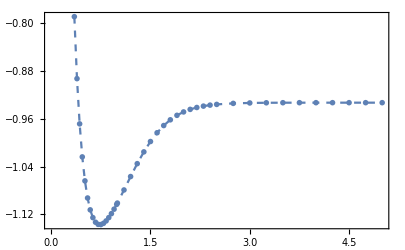

```mathematica
ListPlot[gsH2[[All,{"distance","groundstate"}]],PlotMarkers->{"OpenMarkers",6},PlotStyle->Dashed,Joined->True,Frame->True]
```

## VQE on the virtual device using random ansatz methode

### (0) Original noisy setting: H2onSQC0.mx

Compilation with automatically generated ansatz at Wed 22 Feb 2023 11:48:43 with grad NGAN

@cycle1:Wed 22 Feb 2023 11:50:35, fev:557, <E>: 0.11389992877254461 nansatz: 5 merged-smallθ-metric-bf-gmerged: {0, 3, 0, 8, 22}

@cycle2:Wed 22 Feb 2023 11:52:49, fev:1164, <E>: 0.5128583954341833 nansatz: 14 merged-smallθ-metric-bf-gmerged: {0, 12, 0, 8, 43}

@cycle3:Wed 22 Feb 2023 11:57:08, fev:1958, <E>: 0.21738906509099026 nansatz: 12 merged-smallθ-metric-bf-gmerged: {0, 29, 0, 25, 64}

@cycle4:Wed 22 Feb 2023 12:00:14, fev:2661, <E>: -0.5131501169413366 nansatz: 5 merged-smallθ-metric-bf-gmerged: {0, 46, 0, 37, 81}

Slowing down @cycle 5

@cycle5:Wed 22 Feb 2023 12:01:29, fev:3065, <E>: -0.5131501169413366 nansatz: 5 merged-smallθ-metric-bf-gmerged: {0, 46, 0, 37, 90}

@cycle6:Wed 22 Feb 2023 12:03:40, fev:3795, <E>: -0.5282351582474862 nansatz: 14 merged-smallθ-metric-bf-gmerged: {0, 56, 0, 40, 101}

Slowing down @cycle 7

@cycle7:Wed 22 Feb 2023 12:05:44, fev:4271, <E>: -0.5282351582474862 nansatz: 14 merged-smallθ-metric-bf-gmerged: {0, 56, 0, 40, 106}

Slowing down @cycle 8

@cycle8:Wed 22 Feb 2023 12:09:00, fev:4954, <E>: -0.5282351582474862 nansatz: 14 merged-smallθ-metric-bf-gmerged: {0, 56, 0, 40, 115}

dist 0.35 ; runtime 20.3715 min ; ϵ=0.261034

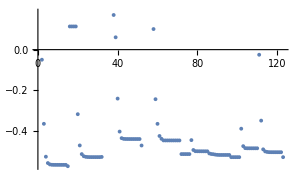

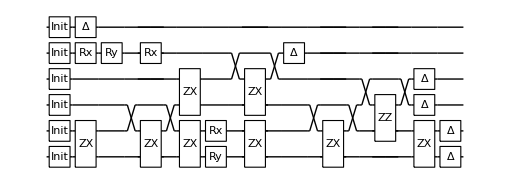

Compilation with automatically generated ansatz at Wed 22 Feb 2023 12:09:06 with grad NGAN

@cycle1:Wed 22 Feb 2023 12:11:00, fev:725, <E>: 0.005177496495294531 nansatz: 18 merged-smallθ-metric-bf-gmerged: {0, 9, 0, 0, 19}

@cycle2:Wed 22 Feb 2023 12:14:32, fev:1572, <E>: -0.5331826877356455 nansatz: 12 merged-smallθ-metric-bf-gmerged: {0, 27, 0, 14, 35}

@cycle3:Wed 22 Feb 2023 12:16:40, fev:2222, <E>: -0.03607574663097446 nansatz: 23 merged-smallθ-metric-bf-gmerged: {0, 34, 0, 14, 40}

@cycle4:Wed 22 Feb 2023 12:20:23, fev:2923, <E>: -0.6196385821300243 nansatz: 6 merged-smallθ-metric-bf-gmerged: {0, 49, 0, 31, 50}

@cycle5:Wed 22 Feb 2023 12:22:01, fev:3565, <E>: -0.044610571484851064 nansatz: 8 merged-smallθ-metric-bf-gmerged: {0, 53, 0, 38, 54}

@cycle6:Wed 22 Feb 2023 12:24:11, fev:4159, <E>: -0.6847072109160933 nansatz: 2 merged-smallθ-metric-bf-gmerged: {0, 65, 0, 61, 68}

Slowing down @cycle 7

@cycle7:Wed 22 Feb 2023 12:25:02, fev:4486, <E>: -0.6847072109160933 nansatz: 2 merged-smallθ-metric-bf-gmerged: {0, 65, 0, 61, 84}

Slowing down @cycle 8

@cycle8:Wed 22 Feb 2023 12:26:19, fev:4935, <E>: -0.6847072109160933 nansatz: 2 merged-smallθ-metric-bf-gmerged: {0, 65, 0, 61, 98}

dist 0.39 ; runtime 17.2282 min ; ϵ=0.208255

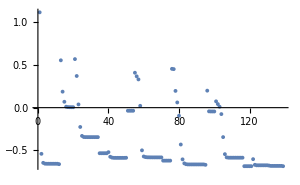

-Graphics-

Compilation with automatically generated ansatz at Wed 22 Feb 2023 12:26:20 with grad NGAN

@cycle1:Wed 22 Feb 2023 12:28:04, fev:625, <E>: -0.7679602878061405 nansatz: 4 merged-smallθ-metric-bf-gmerged: {0, 2, 4, 13, 21}

Slowing down @cycle 2

@cycle2:Wed 22 Feb 2023 12:29:55, fev:1086, <E>: -0.7679602878061405 nansatz: 4 merged-smallθ-metric-bf-gmerged: {0, 2, 4, 13, 45}

Slowing down @cycle 3

@cycle3:Wed 22 Feb 2023 12:32:49, fev:1650, <E>: -0.7679602878061405 nansatz: 4 merged-smallθ-metric-bf-gmerged: {0, 2, 4, 13, 75}

dist 0.43 ; runtime 6.51862 min ; ϵ=0.200646

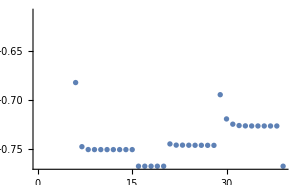

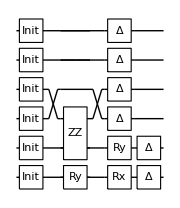

Compilation with automatically generated ansatz at Wed 22 Feb 2023 12:32:51 with grad NGAN

@cycle1:Wed 22 Feb 2023 12:34:20, fev:603, <E>: -0.8303724379422938 nansatz: 4 merged-smallθ-metric-bf-gmerged: {0, 4, 1, 15, 19}

Slowing down @cycle 2

@cycle2:Wed 22 Feb 2023 12:36:05, fev:1031, <E>: -0.8303724379422938 nansatz: 4 merged-smallθ-metric-bf-gmerged: {0, 4, 1, 15, 32}

Slowing down @cycle 3

@cycle3:Wed 22 Feb 2023 12:38:35, fev:1573, <E>: -0.8303724379422938 nansatz: 4 merged-smallθ-metric-bf-gmerged: {0, 4, 1, 15, 57}

dist 0.47 ; runtime 5.75235 min ; ϵ=0.193501

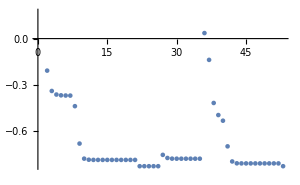

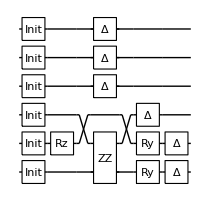

Compilation with automatically generated ansatz at Wed 22 Feb 2023 12:38:36 with grad NGAN

@cycle1:Wed 22 Feb 2023 12:40:11, fev:547, <E>: -0.2661816399952759 nansatz: 10 merged-smallθ-metric-bf-gmerged: {0, 4, 0, 0, 19}

@cycle2:Wed 22 Feb 2023 12:42:40, fev:1136, <E>: -0.8771371862578896 nansatz: 2 merged-smallθ-metric-bf-gmerged: {0, 25, 0, 4, 38}

Slowing down @cycle 3

@cycle3:Wed 22 Feb 2023 12:43:29, fev:1509, <E>: -0.8771371862578896 nansatz: 2 merged-smallθ-metric-bf-gmerged: {0, 25, 0, 4, 49}

Slowing down @cycle 4

@cycle4:Wed 22 Feb 2023 12:44:32, fev:1938, <E>: -0.8771371862578896 nansatz: 2 merged-smallθ-metric-bf-gmerged: {0, 25, 0, 4, 69}

dist 0.51 ; runtime 5.93132 min ; ϵ=0.186853

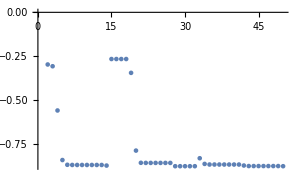

-Graphics-

Compilation with automatically generated ansatz at Wed 22 Feb 2023 12:44:32 with grad NGAN

@cycle1:Wed 22 Feb 2023 12:46:13, fev:635, <E>: -0.9119178624537561 nansatz: 6 merged-smallθ-metric-bf-gmerged: {1, 7, 0, 9, 21}

Slowing down @cycle 2

@cycle2:Wed 22 Feb 2023 12:47:57, fev:1085, <E>: -0.9119178624537561 nansatz: 6 merged-smallθ-metric-bf-gmerged: {1, 7, 0, 9, 41}

Slowing down @cycle 3

@cycle3:Wed 22 Feb 2023 12:50:34, fev:1639, <E>: -0.9119178624537561 nansatz: 6 merged-smallθ-metric-bf-gmerged: {1, 7, 0, 9, 56}

dist 0.55 ; runtime 6.07898 min ; ϵ=0.180712

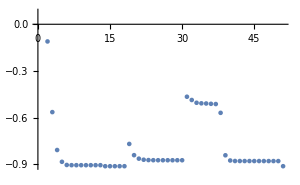

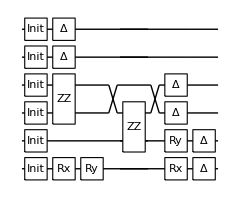

Compilation with automatically generated ansatz at Wed 22 Feb 2023 12:50:37 with grad NGAN

@cycle1:Wed 22 Feb 2023 12:52:08, fev:587, <E>: -0.2060393509539169 nansatz: 16 merged-smallθ-metric-bf-gmerged: {0, 10, 0, 0, 22}

@cycle2:Wed 22 Feb 2023 12:54:33, fev:1268, <E>: -0.9373802846742532 nansatz: 2 merged-smallθ-metric-bf-gmerged: {0, 31, 0, 17, 31}

Slowing down @cycle 3

@cycle3:Wed 22 Feb 2023 12:55:16, fev:1598, <E>: -0.9373802846742532 nansatz: 2 merged-smallθ-metric-bf-gmerged: {0, 31, 0, 17, 42}

Slowing down @cycle 4

@cycle4:Wed 22 Feb 2023 12:56:27, fev:2079, <E>: -0.9373802846742532 nansatz: 2 merged-smallθ-metric-bf-gmerged: {0, 31, 0, 17, 65}

dist 0.59 ; runtime 5.83269 min ; ϵ=0.17508

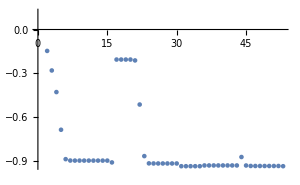

-Graphics-

Compilation with automatically generated ansatz at Wed 22 Feb 2023 12:56:27 with grad NGAN

@cycle1:Wed 22 Feb 2023 12:58:04, fev:553, <E>: -0.9555190461533393 nansatz: 4 merged-smallθ-metric-bf-gmerged: {0, 9, 0, 2, 20}

Slowing down @cycle 2

@cycle2:Wed 22 Feb 2023 12:59:33, fev:983, <E>: -0.9555190461533393 nansatz: 4 merged-smallθ-metric-bf-gmerged: {0, 9, 0, 2, 43}

Slowing down @cycle 3

@cycle3:Wed 22 Feb 2023 13:01:54, fev:1535, <E>: -0.9555190461533393 nansatz: 4 merged-smallθ-metric-bf-gmerged: {0, 9, 0, 2, 65}

dist 0.63 ; runtime 5.46629 min ; ϵ=0.169951

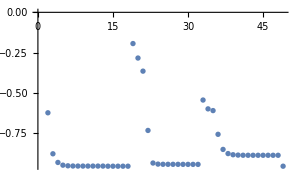

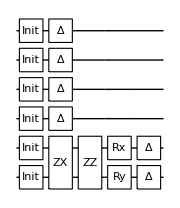

Compilation with automatically generated ansatz at Wed 22 Feb 2023 13:01:55 with grad NGAN

@cycle1:Wed 22 Feb 2023 13:03:30, fev:542, <E>: -0.9496565477129557 nansatz: 13 merged-smallθ-metric-bf-gmerged: {0, 4, 0, 0, 17}

Slowing down @cycle 2

@cycle2:Wed 22 Feb 2023 13:05:41, fev:953, <E>: -0.9496565477129557 nansatz: 13 merged-smallθ-metric-bf-gmerged: {0, 4, 0, 0, 34}

Slowing down @cycle 3

@cycle3:Wed 22 Feb 2023 13:08:55, fev:1521, <E>: -0.9496565477129557 nansatz: 13 merged-smallθ-metric-bf-gmerged: {0, 4, 0, 0, 57}

dist 0.67 ; runtime 7.11968 min ; ϵ=0.183518

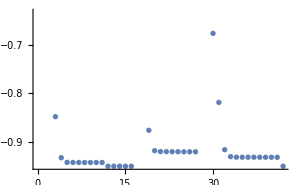

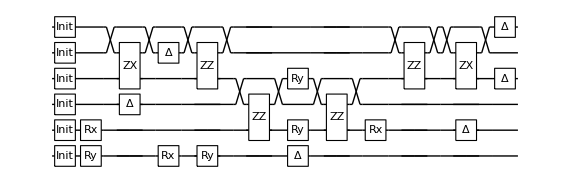

Compilation with automatically generated ansatz at Wed 22 Feb 2023 13:09:02 with grad NGAN

@cycle1:Wed 22 Feb 2023 13:10:42, fev:554, <E>: -0.4462517466071474 nansatz: 5 merged-smallθ-metric-bf-gmerged: {1, 4, 0, 6, 22}

@cycle2:Wed 22 Feb 2023 13:12:26, fev:1041, <E>: -0.43621203154363697 nansatz: 2 merged-smallθ-metric-bf-gmerged: {1, 18, 0, 17, 37}

@cycle3:Wed 22 Feb 2023 13:14:20, fev:1629, <E>: -0.9755966054107332 nansatz: 2 merged-smallθ-metric-bf-gmerged: {1, 34, 0, 27, 46}

Slowing down @cycle 4

@cycle4:Wed 22 Feb 2023 13:15:08, fev:1966, <E>: -0.9755966054107332 nansatz: 2 merged-smallθ-metric-bf-gmerged: {1, 34, 0, 27, 56}

Slowing down @cycle 5

@cycle5:Wed 22 Feb 2023 13:16:27, fev:2471, <E>: -0.9755966054107332 nansatz: 2 merged-smallθ-metric-bf-gmerged: {1, 34, 0, 27, 80}

dist 0.71 ; runtime 7.42127 min ; ϵ=0.161154

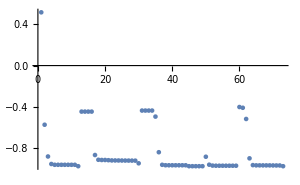

-Graphics-

Compilation with automatically generated ansatz at Wed 22 Feb 2023 13:16:28 with grad NGAN

@cycle1:Wed 22 Feb 2023 13:18:01, fev:549, <E>: -0.9796595478362362 nansatz: 2 merged-smallθ-metric-bf-gmerged: {1, 7, 2, 11, 22}

Slowing down @cycle 2

@cycle2:Wed 22 Feb 2023 13:19:14, fev:905, <E>: -0.9796595478362362 nansatz: 2 merged-smallθ-metric-bf-gmerged: {1, 7, 2, 11, 53}

Slowing down @cycle 3

@cycle3:Wed 22 Feb 2023 13:21:16, fev:1357, <E>: -0.9796595478362362 nansatz: 2 merged-smallθ-metric-bf-gmerged: {1, 7, 2, 11, 85}

dist 0.75 ; runtime 4.80318 min ; ϵ=0.157458

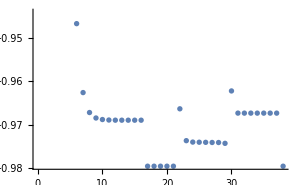

-Graphics-

Compilation with automatically generated ansatz at Wed 22 Feb 2023 13:21:16 with grad NGAN

@cycle1:Wed 22 Feb 2023 13:22:52, fev:579, <E>: -0.49628540720513636 nansatz: 11 merged-smallθ-metric-bf-gmerged: {2, 6, 0, 0, 22}

@cycle2:Wed 22 Feb 2023 13:25:11, fev:1210, <E>: -0.9807889071875866 nansatz: 2 merged-smallθ-metric-bf-gmerged: {2, 21, 0, 18, 36}

Slowing down @cycle 3

@cycle3:Wed 22 Feb 2023 13:26:01, fev:1559, <E>: -0.9807889071875866 nansatz: 2 merged-smallθ-metric-bf-gmerged: {2, 21, 0, 18, 58}

Slowing down @cycle 4

@cycle4:Wed 22 Feb 2023 13:27:15, fev:2030, <E>: -0.9807889071875866 nansatz: 2 merged-smallθ-metric-bf-gmerged: {2, 21, 0, 18, 66}

dist 0.79 ; runtime 5.9808 min ; ϵ=0.154208

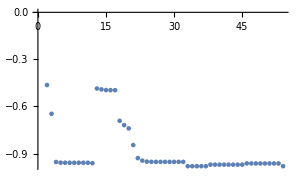

-Graphics-

Compilation with automatically generated ansatz at Wed 22 Feb 2023 13:27:15 with grad NGAN

@cycle1:Wed 22 Feb 2023 13:29:02, fev:637, <E>: -0.5235151340066458 nansatz: 25 merged-smallθ-metric-bf-gmerged: {0, 2, 0, 0, 16}

@cycle2:Wed 22 Feb 2023 13:32:44, fev:1321, <E>: -0.49202829184812735 nansatz: 1 merged-smallθ-metric-bf-gmerged: {0, 33, 0, 9, 36}

@cycle3:Wed 22 Feb 2023 13:34:48, fev:1994, <E>: -0.9123221727286013 nansatz: 19 merged-smallθ-metric-bf-gmerged: {0, 37, 0, 11, 54}

Slowing down @cycle 4

@cycle4:Wed 22 Feb 2023 13:36:42, fev:2369, <E>: -0.9123221727286013 nansatz: 19 merged-smallθ-metric-bf-gmerged: {0, 37, 0, 11, 62}

@cycle5:Wed 22 Feb 2023 13:40:44, fev:3349, <E>: -0.49079490489916433 nansatz: 27 merged-smallθ-metric-bf-gmerged: {0, 51, 0, 11, 67}

@cycle6:Wed 22 Feb 2023 13:46:34, fev:4189, <E>: -0.44228617021886696 nansatz: 10 merged-smallθ-metric-bf-gmerged: {1, 77, 0, 11, 85}

@cycle7:Wed 22 Feb 2023 13:50:46, fev:4989, <E>: -0.5003108522661643 nansatz: 14 merged-smallθ-metric-bf-gmerged: {1, 99, 0, 11, 115}

@cycle8:Wed 22 Feb 2023 13:55:07, fev:5905, <E>: -0.9596914722778618 nansatz: 14 merged-smallθ-metric-bf-gmerged: {1, 120, 0, 21, 138}

@cycle9:Wed 22 Feb 2023 13:57:55, fev:6656, <E>: -0.9691454549736909 nansatz: 24 merged-smallθ-metric-bf-gmerged: {1, 123, 0, 25, 144}

Slowing down @cycle 10

@cycle10:Wed 22 Feb 2023 14:01:02, fev:7225, <E>: -0.9691454549736909 nansatz: 24 merged-smallθ-metric-bf-gmerged: {1, 123, 0, 25, 155}

Slowing down @cycle 11

@cycle11:Wed 22 Feb 2023 14:05:26, fev:7924, <E>: -0.9691454549736909 nansatz: 24 merged-smallθ-metric-bf-gmerged: {1, 123, 0, 25, 173}

dist 0.83 ; runtime 38.557 min ; ϵ=0.161812

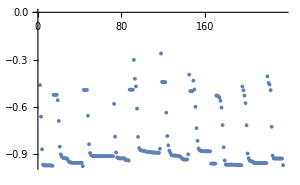

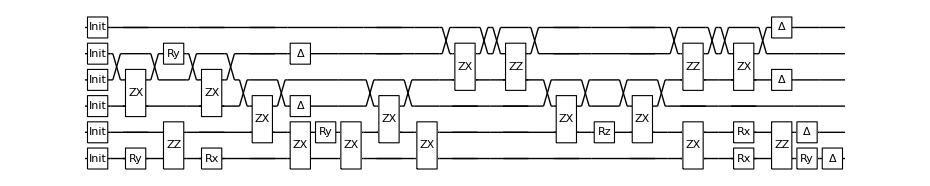

Compilation with automatically generated ansatz at Wed 22 Feb 2023 14:05:48 with grad NGAN

@cycle1:Wed 22 Feb 2023 14:07:20, fev:581, <E>: -0.9764374891505784 nansatz: 10 merged-smallθ-metric-bf-gmerged: {0, 5, 0, 9, 14}

Slowing down @cycle 2

@cycle2:Wed 22 Feb 2023 14:09:00, fev:966, <E>: -0.9764374891505784 nansatz: 10 merged-smallθ-metric-bf-gmerged: {0, 5, 0, 9, 33}

Slowing down @cycle 3

@cycle3:Wed 22 Feb 2023 14:11:43, fev:1502, <E>: -0.9764374891505784 nansatz: 10 merged-smallθ-metric-bf-gmerged: {0, 5, 0, 9, 55}

dist 0.87 ; runtime 5.95115 min ; ϵ=0.149008

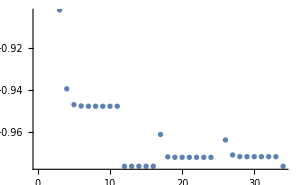

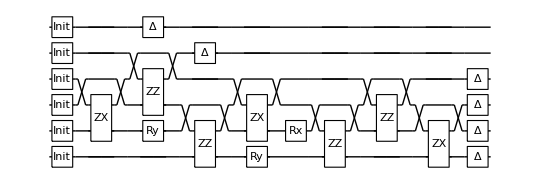

Compilation with automatically generated ansatz at Wed 22 Feb 2023 14:11:46 with grad NGAN

@cycle1:Wed 22 Feb 2023 14:13:10, fev:549, <E>: -0.9718284603720583 nansatz: 2 merged-smallθ-metric-bf-gmerged: {0, 1, 0, 20, 22}

Slowing down @cycle 2

@cycle2:Wed 22 Feb 2023 14:14:44, fev:994, <E>: -0.9718284603720583 nansatz: 2 merged-smallθ-metric-bf-gmerged: {0, 1, 0, 20, 45}

Slowing down @cycle 3

@cycle3:Wed 22 Feb 2023 14:17:00, fev:1531, <E>: -0.9718284603720583 nansatz: 2 merged-smallθ-metric-bf-gmerged: {0, 1, 0, 20, 70}

dist 0.91 ; runtime 5.23702 min ; ϵ=0.146985

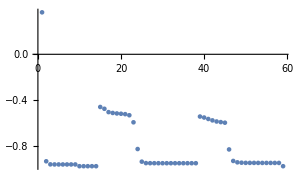

-Graphics-

Compilation with automatically generated ansatz at Wed 22 Feb 2023 14:17:00 with grad NGAN

@cycle1:Wed 22 Feb 2023 14:18:29, fev:612, <E>: -0.9631963728287849 nansatz: 13 merged-smallθ-metric-bf-gmerged: {0, 1, 0, 15, 30}

Slowing down @cycle 2

@cycle2:Wed 22 Feb 2023 14:20:16, fev:1008, <E>: -0.9631963728287849 nansatz: 13 merged-smallθ-metric-bf-gmerged: {0, 1, 0, 15, 52}

Slowing down @cycle 3

@cycle3:Wed 22 Feb 2023 14:23:12, fev:1552, <E>: -0.9631963728287849 nansatz: 13 merged-smallθ-metric-bf-gmerged: {0, 1, 0, 15, 77}

dist 0.95 ; runtime 6.2795 min ; ϵ=0.148143

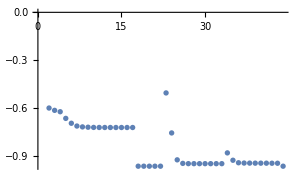

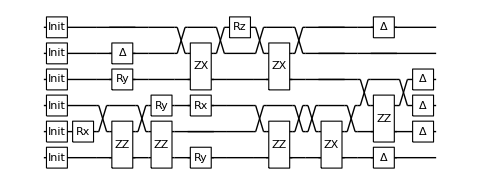

Compilation with automatically generated ansatz at Wed 22 Feb 2023 14:23:17 with grad NGAN

@cycle1:Wed 22 Feb 2023 14:24:51, fev:591, <E>: -0.9271056655877611 nansatz: 11 merged-smallθ-metric-bf-gmerged: {1, 3, 0, 0, 13}

Slowing down @cycle 2

@cycle2:Wed 22 Feb 2023 14:27:12, fev:1055, <E>: -0.9271056655877611 nansatz: 11 merged-smallθ-metric-bf-gmerged: {1, 3, 0, 0, 25}

Slowing down @cycle 3

@cycle3:Wed 22 Feb 2023 14:30:31, fev:1607, <E>: -0.9271056655877611 nansatz: 11 merged-smallθ-metric-bf-gmerged: {1, 3, 0, 0, 44}

dist 0.99 ; runtime 7.37406 min ; ϵ=0.147359

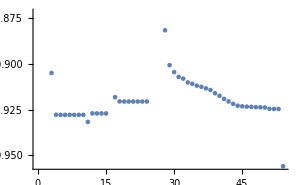

-Graphics-

Compilation with automatically generated ansatz at Wed 22 Feb 2023 14:30:39 with grad NGAN

@cycle1:Wed 22 Feb 2023 14:32:37, fev:643, <E>: -0.5919387069548396 nansatz: 9 merged-smallθ-metric-bf-gmerged: {0, 2, 2, 14, 20}

@cycle2:Wed 22 Feb 2023 14:35:24, fev:1324, <E>: -0.9566925875478869 nansatz: 4 merged-smallθ-metric-bf-gmerged: {0, 16, 2, 28, 32}

Slowing down @cycle 3

@cycle3:Wed 22 Feb 2023 14:36:41, fev:1744, <E>: -0.9566925875478869 nansatz: 4 merged-smallθ-metric-bf-gmerged: {0, 16, 2, 28, 45}

Slowing down @cycle 4

@cycle4:Wed 22 Feb 2023 14:38:04, fev:2185, <E>: -0.9566925875478869 nansatz: 4 merged-smallθ-metric-bf-gmerged: {0, 16, 2, 28, 71}

dist 1. ; runtime 7.42444 min ; ϵ=0.144458

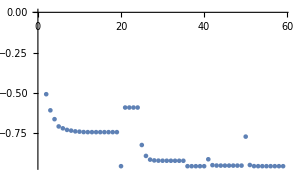

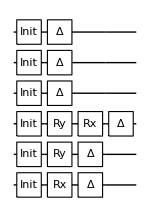

Compilation with automatically generated ansatz at Wed 22 Feb 2023 14:38:05 with grad NGAN

@cycle1:Wed 22 Feb 2023 14:39:42, fev:620, <E>: -0.9361600295842243 nansatz: 7 merged-smallθ-metric-bf-gmerged: {0, 2, 0, 12, 13}

Slowing down @cycle 2

@cycle2:Wed 22 Feb 2023 14:41:33, fev:1005, <E>: -0.9361600295842243 nansatz: 7 merged-smallθ-metric-bf-gmerged: {0, 2, 0, 12, 29}

Slowing down @cycle 3

@cycle3:Wed 22 Feb 2023 14:44:27, fev:1535, <E>: -0.9361600295842243 nansatz: 7 merged-smallθ-metric-bf-gmerged: {0, 2, 0, 12, 44}

dist 1.1 ; runtime 6.3866 min ; ϵ=0.143033

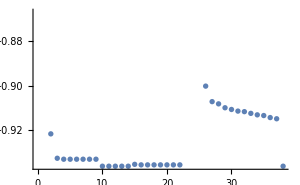

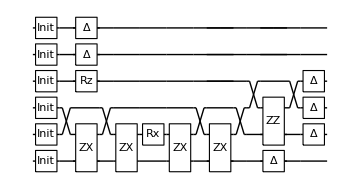

Compilation with automatically generated ansatz at Wed 22 Feb 2023 14:44:28 with grad NGAN

@cycle1:Wed 22 Feb 2023 14:45:46, fev:486, <E>: -0.9116029648510324 nansatz: 9 merged-smallθ-metric-bf-gmerged: {0, 0, 0, 3, 24}

Slowing down @cycle 2

@cycle2:Wed 22 Feb 2023 14:47:52, fev:943, <E>: -0.9116029648510324 nansatz: 9 merged-smallθ-metric-bf-gmerged: {0, 0, 0, 3, 45}

Slowing down @cycle 3

@cycle3:Wed 22 Feb 2023 14:50:36, fev:1460, <E>: -0.9116029648510324 nansatz: 9 merged-smallθ-metric-bf-gmerged: {0, 0, 0, 3, 64}

dist 1.2 ; runtime 6.19221 min ; ϵ=0.145138

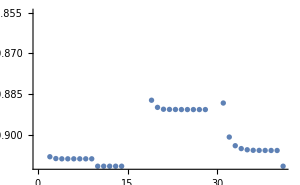

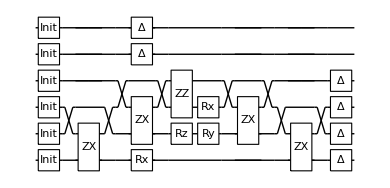

Compilation with automatically generated ansatz at Wed 22 Feb 2023 14:50:40 with grad NGAN

@cycle1:Wed 22 Feb 2023 14:52:41, fev:582, <E>: -0.7728531112267558 nansatz: 2 merged-smallθ-metric-bf-gmerged: {2, 2, 2, 11, 22}

Slowing down @cycle 2

@cycle2:Wed 22 Feb 2023 14:54:20, fev:965, <E>: -0.7728531112267558 nansatz: 2 merged-smallθ-metric-bf-gmerged: {2, 2, 2, 11, 39}

Slowing down @cycle 3

@cycle3:Wed 22 Feb 2023 14:57:10, fev:1535, <E>: -0.7728531112267558 nansatz: 2 merged-smallθ-metric-bf-gmerged: {2, 2, 2, 11, 54}

dist 1.3 ; runtime 6.50525 min ; ϵ=0.262333

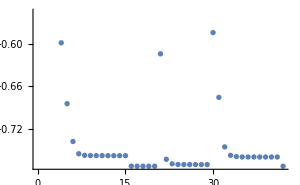

-Graphics-

Compilation with automatically generated ansatz at Wed 22 Feb 2023 14:57:10 with grad NGAN

@cycle1:Wed 22 Feb 2023 14:58:40, fev:499, <E>: -0.8542356684243385 nansatz: 12 merged-smallθ-metric-bf-gmerged: {1, 8, 0, 0, 17}

Slowing down @cycle 2

@cycle2:Wed 22 Feb 2023 15:00:48, fev:925, <E>: -0.8542356684243385 nansatz: 12 merged-smallθ-metric-bf-gmerged: {1, 8, 0, 0, 35}

Slowing down @cycle 3

@cycle3:Wed 22 Feb 2023 15:04:17, fev:1498, <E>: -0.8542356684243385 nansatz: 12 merged-smallθ-metric-bf-gmerged: {1, 8, 0, 0, 66}

dist 1.4 ; runtime 7.20287 min ; ϵ=0.152729

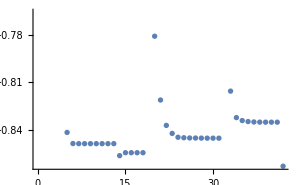

-Graphics-

Compilation with automatically generated ansatz at Wed 22 Feb 2023 15:04:22 with grad NGAN

@cycle1:Wed 22 Feb 2023 15:06:16, fev:656, <E>: -0.827521486301441 nansatz: 16 merged-smallθ-metric-bf-gmerged: {0, 0, 0, 8, 25}

@cycle2:Wed 22 Feb 2023 15:09:24, fev:1387, <E>: -0.8471537544868788 nansatz: 13 merged-smallθ-metric-bf-gmerged: {0, 18, 0, 17, 38}

@cycle3:Wed 22 Feb 2023 15:12:32, fev:2178, <E>: -0.7883088370468405 nansatz: 18 merged-smallθ-metric-bf-gmerged: {0, 25, 0, 27, 54}

@cycle4:Wed 22 Feb 2023 15:16:33, fev:2876, <E>: -0.8378825790946983 nansatz: 2 merged-smallθ-metric-bf-gmerged: {0, 48, 0, 40, 69}

@cycle5:Wed 22 Feb 2023 15:18:26, fev:3443, <E>: -0.8630398541410226 nansatz: 15 merged-smallθ-metric-bf-gmerged: {0, 52, 0, 43, 96}

Slowing down @cycle 6

@cycle6:Wed 22 Feb 2023 15:21:11, fev:3918, <E>: -0.8630398541410226 nansatz: 15 merged-smallθ-metric-bf-gmerged: {0, 52, 0, 43, 113}

Slowing down @cycle 7

@cycle7:Wed 22 Feb 2023 15:25:06, fev:4482, <E>: -0.8630398541410226 nansatz: 15 merged-smallθ-metric-bf-gmerged: {0, 52, 0, 43, 132}

dist 1.5 ; runtime 20.9833 min ; ϵ=0.135109

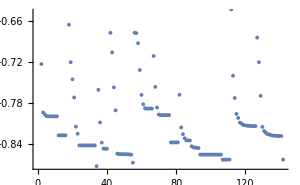

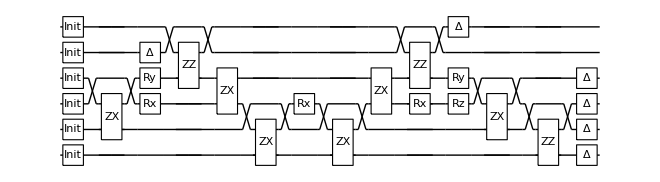

Compilation with automatically generated ansatz at Wed 22 Feb 2023 15:25:21 with grad NGAN

@cycle1:Wed 22 Feb 2023 15:26:47, fev:491, <E>: -0.8201986859451103 nansatz: 9 merged-smallθ-metric-bf-gmerged: {0, 5, 0, 8, 21}

Slowing down @cycle 2

@cycle2:Wed 22 Feb 2023 15:28:36, fev:889, <E>: -0.8201986859451103 nansatz: 9 merged-smallθ-metric-bf-gmerged: {0, 5, 0, 8, 29}

Slowing down @cycle 3

@cycle3:Wed 22 Feb 2023 15:31:43, fev:1446, <E>: -0.8201986859451103 nansatz: 9 merged-smallθ-metric-bf-gmerged: {0, 5, 0, 8, 43}

dist 1.6 ; runtime 6.4228 min ; ϵ=0.163274

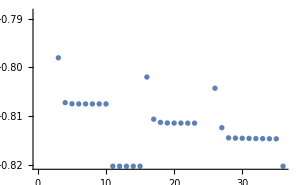

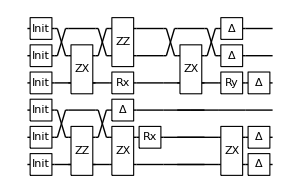

Compilation with automatically generated ansatz at Wed 22 Feb 2023 15:31:47 with grad NGAN

@cycle1:Wed 22 Feb 2023 15:33:22, fev:464, <E>: -0.7912215933255478 nansatz: 2 merged-smallθ-metric-bf-gmerged: {0, 9, 0, 0, 19}

@cycle2:Wed 22 Feb 2023 15:34:58, fev:980, <E>: -0.7880228536352194 nansatz: 9 merged-smallθ-metric-bf-gmerged: {0, 19, 0, 0, 44}

Slowing down @cycle 3

@cycle3:Wed 22 Feb 2023 15:37:05, fev:1394, <E>: -0.7880228536352194 nansatz: 9 merged-smallθ-metric-bf-gmerged: {0, 19, 0, 0, 65}

@cycle4:Wed 22 Feb 2023 15:40:46, fev:2160, <E>: -0.8232422985719907 nansatz: 6 merged-smallθ-metric-bf-gmerged: {0, 32, 0, 18, 84}

Slowing down @cycle 5

@cycle5:Wed 22 Feb 2023 15:43:05, fev:2648, <E>: -0.8232422985719907 nansatz: 6 merged-smallθ-metric-bf-gmerged: {0, 32, 0, 18, 105}

Slowing down @cycle 6

@cycle6:Wed 22 Feb 2023 15:46:30, fev:3279, <E>: -0.8232422985719907 nansatz: 6 merged-smallθ-metric-bf-gmerged: {0, 32, 0, 18, 135}

dist 1.7 ; runtime 14.7413 min ; ϵ=0.148184

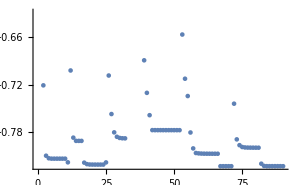

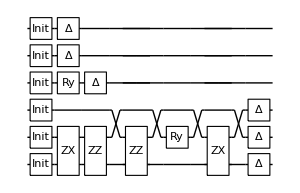

Compilation with automatically generated ansatz at Wed 22 Feb 2023 15:46:31 with grad NGAN

@cycle1:Wed 22 Feb 2023 15:48:03, fev:518, <E>: -0.8358596523237729 nansatz: 2 merged-smallθ-metric-bf-gmerged: {0, 13, 0, 1, 22}

Slowing down @cycle 2

@cycle2:Wed 22 Feb 2023 15:49:31, fev:921, <E>: -0.8358596523237729 nansatz: 2 merged-smallθ-metric-bf-gmerged: {0, 13, 0, 1, 36}

Slowing down @cycle 3

@cycle3:Wed 22 Feb 2023 15:51:29, fev:1381, <E>: -0.8358596523237729 nansatz: 2 merged-smallθ-metric-bf-gmerged: {0, 13, 0, 1, 63}

dist 1.8 ; runtime 4.96984 min ; ϵ=0.125957

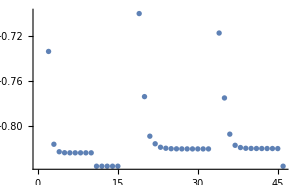

-Graphics-

Compilation with automatically generated ansatz at Wed 22 Feb 2023 15:51:30 with grad NGAN

@cycle1:Wed 22 Feb 2023 15:53:08, fev:527, <E>: -0.4877162614400932 nansatz: 4 merged-smallθ-metric-bf-gmerged: {0, 13, 0, 0, 16}

@cycle2:Wed 22 Feb 2023 15:55:10, fev:1094, <E>: -0.8341643792121857 nansatz: 2 merged-smallθ-metric-bf-gmerged: {0, 31, 0, 14, 35}

Slowing down @cycle 3

@cycle3:Wed 22 Feb 2023 15:56:07, fev:1479, <E>: -0.8341643792121857 nansatz: 2 merged-smallθ-metric-bf-gmerged: {0, 31, 0, 14, 42}

Slowing down @cycle 4

@cycle4:Wed 22 Feb 2023 15:57:18, fev:1922, <E>: -0.8341643792121857 nansatz: 2 merged-smallθ-metric-bf-gmerged: {0, 31, 0, 14, 55}

dist 1.9 ; runtime 5.80548 min ; ϵ=0.120174

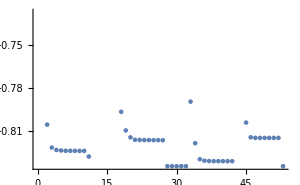

-Graphics-

Compilation with automatically generated ansatz at Wed 22 Feb 2023 15:57:18 with grad NGAN

@cycle1:Wed 22 Feb 2023 15:58:53, fev:639, <E>: -0.8356673864573043 nansatz: 6 merged-smallθ-metric-bf-gmerged: {0, 6, 1, 17, 10}

Slowing down @cycle 2

@cycle2:Wed 22 Feb 2023 16:00:28, fev:1035, <E>: -0.8356673864573043 nansatz: 6 merged-smallθ-metric-bf-gmerged: {0, 6, 1, 17, 26}

Slowing down @cycle 3

@cycle3:Wed 22 Feb 2023 16:02:48, fev:1562, <E>: -0.8356673864573043 nansatz: 6 merged-smallθ-metric-bf-gmerged: {0, 6, 1, 17, 47}

dist 2. ; runtime 5.51658 min ; ϵ=0.112974

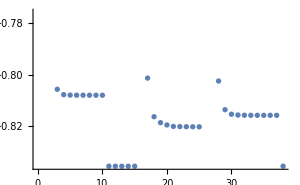

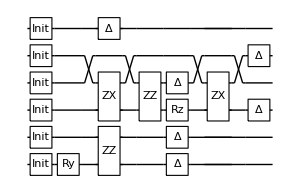

Compilation with automatically generated ansatz at Wed 22 Feb 2023 16:02:49 with grad NGAN

@cycle1:Wed 22 Feb 2023 16:04:24, fev:606, <E>: -0.8405044442934196 nansatz: 9 merged-smallθ-metric-bf-gmerged: {0, 1, 0, 13, 16}

@cycle2:Wed 22 Feb 2023 16:07:03, fev:1379, <E>: -0.8483763124942384 nansatz: 20 merged-smallθ-metric-bf-gmerged: {0, 2, 0, 28, 34}

Slowing down @cycle 3

@cycle3:Wed 22 Feb 2023 16:09:30, fev:1793, <E>: -0.8483763124942384 nansatz: 20 merged-smallθ-metric-bf-gmerged: {0, 2, 0, 28, 50}

Slowing down @cycle 4

@cycle4:Wed 22 Feb 2023 16:13:13, fev:2332, <E>: -0.8483763124942384 nansatz: 20 merged-smallθ-metric-bf-gmerged: {0, 2, 0, 28, 70}

dist 2.1 ; runtime 10.6289 min ; ϵ=0.0959984

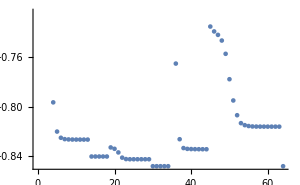

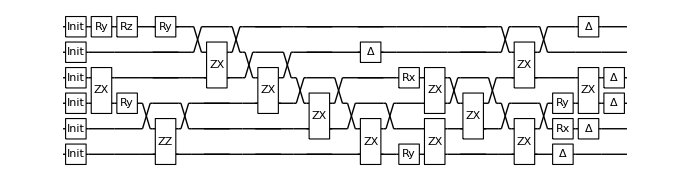

Compilation with automatically generated ansatz at Wed 22 Feb 2023 16:13:27 with grad NGAN

@cycle1:Wed 22 Feb 2023 16:14:44, fev:446, <E>: -0.8432788372005455 nansatz: 4 merged-smallθ-metric-bf-gmerged: {4, 4, 0, 5, 32}

Slowing down @cycle 2

@cycle2:Wed 22 Feb 2023 16:15:59, fev:795, <E>: -0.8432788372005455 nansatz: 4 merged-smallθ-metric-bf-gmerged: {4, 4, 0, 5, 50}

Slowing down @cycle 3

@cycle3:Wed 22 Feb 2023 16:18:29, fev:1310, <E>: -0.8432788372005455 nansatz: 4 merged-smallθ-metric-bf-gmerged: {4, 4, 0, 5, 72}

dist 2.2 ; runtime 5.04503 min ; ϵ=0.0979452

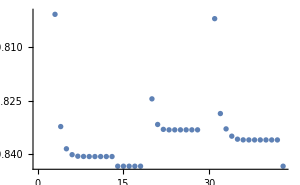

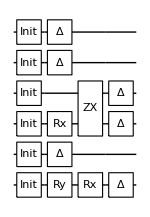

Compilation with automatically generated ansatz at Wed 22 Feb 2023 16:18:30 with grad NGAN

@cycle1:Wed 22 Feb 2023 16:19:47, fev:485, <E>: -0.4736653586280543 nansatz: 2 merged-smallθ-metric-bf-gmerged: {1, 8, 0, 7, 17}

@cycle2:Wed 22 Feb 2023 16:21:34, fev:1118, <E>: -0.6314663102882384 nansatz: 15 merged-smallθ-metric-bf-gmerged: {1, 20, 0, 7, 35}

@cycle3:Wed 22 Feb 2023 16:23:24, fev:1706, <E>: -0.8313632817660703 nansatz: 9 merged-smallθ-metric-bf-gmerged: {1, 28, 0, 26, 46}

@cycle4:Wed 22 Feb 2023 16:24:46, fev:2359, <E>: -0.8423865363165173 nansatz: 11 merged-smallθ-metric-bf-gmerged: {1, 36, 1, 32, 59}

Slowing down @cycle 5

@cycle5:Wed 22 Feb 2023 16:25:42, fev:2675, <E>: -0.8423865363165173 nansatz: 11 merged-smallθ-metric-bf-gmerged: {1, 36, 1, 32, 62}

Slowing down @cycle 6

@cycle6:Wed 22 Feb 2023 16:27:22, fev:3139, <E>: -0.8423865363165173 nansatz: 11 merged-smallθ-metric-bf-gmerged: {1, 36, 1, 32, 80}

dist 2.3 ; runtime 8.90242 min ; ϵ=0.0965358

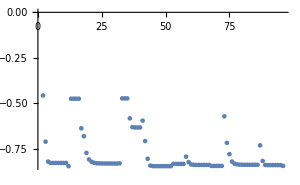

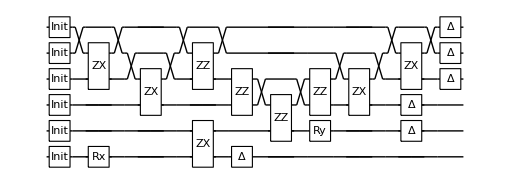

Compilation with automatically generated ansatz at Wed 22 Feb 2023 16:27:24 with grad NGAN

@cycle1:Wed 22 Feb 2023 16:28:54, fev:630, <E>: -0.6240211170776971 nansatz: 16 merged-smallθ-metric-bf-gmerged: {0, 6, 0, 3, 19}

@cycle2:Wed 22 Feb 2023 16:31:12, fev:1266, <E>: -0.5721738386170111 nansatz: 9 merged-smallθ-metric-bf-gmerged: {0, 24, 0, 12, 33}

@cycle3:Wed 22 Feb 2023 16:33:44, fev:1965, <E>: -0.8471420341310937 nansatz: 5 merged-smallθ-metric-bf-gmerged: {0, 36, 0, 23, 52}

Slowing down @cycle 4

@cycle4:Wed 22 Feb 2023 16:34:43, fev:2352, <E>: -0.8471420341310937 nansatz: 5 merged-smallθ-metric-bf-gmerged: {0, 36, 0, 23, 64}

Slowing down @cycle 5

@cycle5:Wed 22 Feb 2023 16:36:09, fev:2803, <E>: -0.8471420341310937 nansatz: 5 merged-smallθ-metric-bf-gmerged: {0, 36, 0, 23, 85}

dist 2.4 ; runtime 8.77592 min ; ϵ=0.0901129

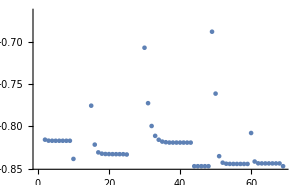

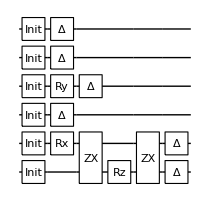

Compilation with automatically generated ansatz at Wed 22 Feb 2023 16:36:11 with grad NGAN

@cycle1:Wed 22 Feb 2023 16:37:36, fev:465, <E>: -0.47919485438331044 nansatz: 5 merged-smallθ-metric-bf-gmerged: {0, 0, 0, 5, 18}

@cycle2:Wed 22 Feb 2023 16:39:24, fev:1026, <E>: -0.4805694247963373 nansatz: 5 merged-smallθ-metric-bf-gmerged: {0, 18, 0, 12, 31}

@cycle3:Wed 22 Feb 2023 16:41:20, fev:1621, <E>: -0.8453591281813538 nansatz: 8 merged-smallθ-metric-bf-gmerged: {0, 28, 0, 22, 40}

Slowing down @cycle 4

@cycle4:Wed 22 Feb 2023 16:42:43, fev:2024, <E>: -0.8453591281813538 nansatz: 8 merged-smallθ-metric-bf-gmerged: {0, 28, 0, 22, 45}

@cycle5:Wed 22 Feb 2023 16:44:54, fev:2732, <E>: -0.8469520578679725 nansatz: 17 merged-smallθ-metric-bf-gmerged: {0, 38, 0, 22, 56}

Slowing down @cycle 6

@cycle6:Wed 22 Feb 2023 16:46:59, fev:3221, <E>: -0.8469520578679725 nansatz: 17 merged-smallθ-metric-bf-gmerged: {0, 38, 0, 22, 60}

Slowing down @cycle 7

@cycle7:Wed 22 Feb 2023 16:50:13, fev:3849, <E>: -0.8469520578679725 nansatz: 17 merged-smallθ-metric-bf-gmerged: {0, 38, 0, 22, 68}

dist 2.5 ; runtime 14.4258 min ; ϵ=0.0889473

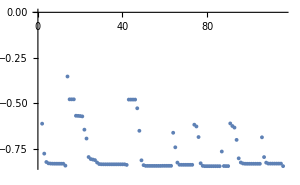

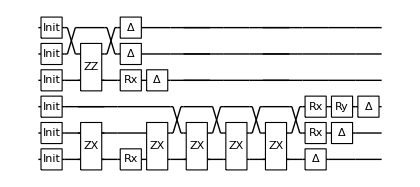

Compilation with automatically generated ansatz at Wed 22 Feb 2023 16:50:37 with grad NGAN

@cycle1:Wed 22 Feb 2023 16:52:02, fev:478, <E>: -0.6198637572882026 nansatz: 2 merged-smallθ-metric-bf-gmerged: {2, 12, 0, 0, 25}

@cycle2:Wed 22 Feb 2023 16:53:27, fev:994, <E>: -0.8466875100867272 nansatz: 2 merged-smallθ-metric-bf-gmerged: {2, 28, 0, 10, 36}

@cycle3:Wed 22 Feb 2023 16:54:31, fev:1496, <E>: -0.8557791366574217 nansatz: 7 merged-smallθ-metric-bf-gmerged: {2, 34, 1, 17, 50}

Slowing down @cycle 4

@cycle4:Wed 22 Feb 2023 16:55:35, fev:1887, <E>: -0.8557791366574217 nansatz: 7 merged-smallθ-metric-bf-gmerged: {2, 34, 1, 17, 61}

Slowing down @cycle 5

@cycle5:Wed 22 Feb 2023 16:57:16, fev:2398, <E>: -0.8557791366574217 nansatz: 7 merged-smallθ-metric-bf-gmerged: {2, 34, 1, 17, 74}

dist 2.75 ; runtime 6.70634 min ; ϵ=0.0785699

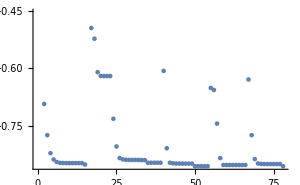

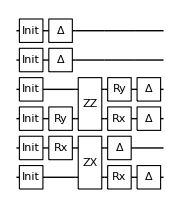

Compilation with automatically generated ansatz at Wed 22 Feb 2023 16:57:19 with grad NGAN

@cycle1:Wed 22 Feb 2023 16:58:51, fev:586, <E>: -0.84652881003001 nansatz: 13 merged-smallθ-metric-bf-gmerged: {0, 6, 0, 8, 14}

Slowing down @cycle 2

@cycle2:Wed 22 Feb 2023 17:01:04, fev:1002, <E>: -0.84652881003001 nansatz: 13 merged-smallθ-metric-bf-gmerged: {0, 6, 0, 8, 41}

Slowing down @cycle 3

@cycle3:Wed 22 Feb 2023 17:04:18, fev:1518, <E>: -0.84652881003001 nansatz: 13 merged-smallθ-metric-bf-gmerged: {0, 6, 0, 8, 59}

dist 3. ; runtime 7.10041 min ; ϵ=0.087103

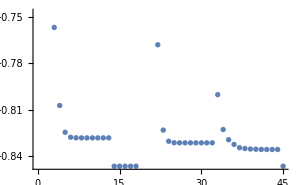

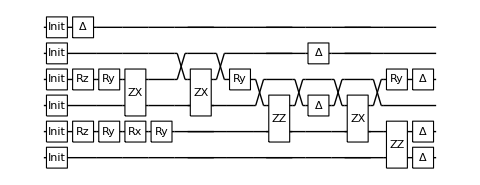

Compilation with automatically generated ansatz at Wed 22 Feb 2023 17:04:25 with grad NGAN

@cycle1:Wed 22 Feb 2023 17:05:50, fev:543, <E>: -0.8516839988375403 nansatz: 13 merged-smallθ-metric-bf-gmerged: {0, 3, 0, 7, 24}

Slowing down @cycle 2

@cycle2:Wed 22 Feb 2023 17:07:47, fev:933, <E>: -0.8516839988375403 nansatz: 13 merged-smallθ-metric-bf-gmerged: {0, 3, 0, 7, 39}

Slowing down @cycle 3

@cycle3:Wed 22 Feb 2023 17:10:51, fev:1475, <E>: -0.8516839988375403 nansatz: 13 merged-smallθ-metric-bf-gmerged: {0, 3, 0, 7, 55}

dist 3.25 ; runtime 6.51256 min ; ϵ=0.0816573

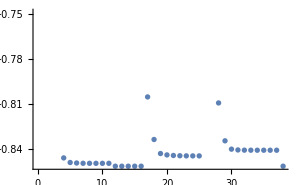

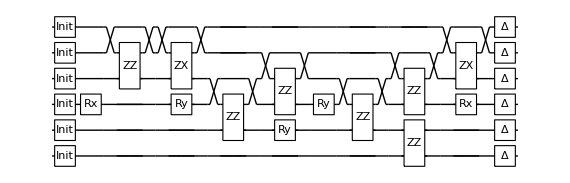

Compilation with automatically generated ansatz at Wed 22 Feb 2023 17:10:56 with grad NGAN

@cycle1:Wed 22 Feb 2023 17:12:36, fev:585, <E>: -0.8364979260943076 nansatz: 13 merged-smallθ-metric-bf-gmerged: {0, 9, 0, 2, 21}

@cycle2:Wed 22 Feb 2023 17:15:15, fev:1214, <E>: -0.4427882069232165 nansatz: 10 merged-smallθ-metric-bf-gmerged: {0, 28, 0, 12, 28}

$Aborted

```mathematica
Table[
 {distance, hamfile, hamiltonian, groundstate} = Values@data;
 dev = SuperconductingHub[];
 conf = DefaultConfig[dev, hamiltonian];
 conf["groundstate"] = groundstate;
    res = VQEonVQD[conf];
 {runtime, cost, Elist, ansatz, θvars, finmsg, ncycle, fev, aborted, cycleres, elimmerge, elimbfsmall, elimmetov, elimbf} = res;
 AppendTo[H2onSQC0, <|"runtime" -> runtime, "ansatz" -> ansatz, "θvars" -> θvars, "groundstate" -> groundstate, "cost" -> cost, "fev" -> fev|>];
 DumpSave["H2onSQC0.mx", H2onSQC0];
 Print["dist ", distance, " ; runtime ", runtime, " ; ϵ=", Last@Elist - conf["groundstate"]];
 Print[ListPlot[Elist, ImageSize -> 300]];
 Print[DrawCircuit[ansatz, 6]];
 , {data, gsH2}]
```

Compilation with automatically generated ansatz at Thu 23 Feb 2023 13:22:57 with grad NGAN

@cycle1:Thu 23 Feb 2023 13:24:56, fev:561, <E>: -0.8518587779064822 nansatz: 2 merged-smallθ-metric-bf-gmerged: {2, 7, 0, 5, 10}

Slowing down @cycle 2

@cycle2:Thu 23 Feb 2023 13:26:30, fev:931, <E>: -0.8518587779064822 nansatz: 2 merged-smallθ-metric-bf-gmerged: {2, 7, 0, 5, 22}

Slowing down @cycle 3

@cycle3:Thu 23 Feb 2023 13:29:03, fev:1451, <E>: -0.8518587779064822 nansatz: 2 merged-smallθ-metric-bf-gmerged: {2, 7, 0, 5, 30}

dist 3.5 ; runtime 6.14887 min ; ϵ=0.0813696

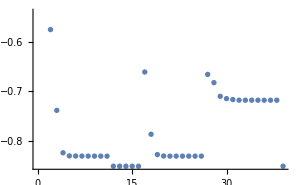

-Graphics-

Compilation with automatically generated ansatz at Thu 23 Feb 2023 13:29:06 with grad NGAN

@cycle1:Thu 23 Feb 2023 13:31:12, fev:619, <E>: -0.8448344036286108 nansatz: 8 merged-smallθ-metric-bf-gmerged: {0, 4, 0, 5, 10}

Slowing down @cycle 2

@cycle2:Thu 23 Feb 2023 13:33:18, fev:1005, <E>: -0.8448344036286108 nansatz: 8 merged-smallθ-metric-bf-gmerged: {0, 4, 0, 5, 22}

Slowing down @cycle 3

@cycle3:Thu 23 Feb 2023 13:36:02, fev:1458, <E>: -0.8448344036286108 nansatz: 8 merged-smallθ-metric-bf-gmerged: {0, 4, 0, 5, 32}

dist 3.75 ; runtime 7.08059 min ; ϵ=0.088352

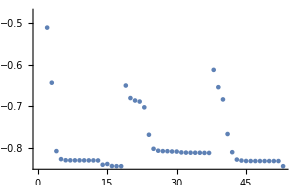

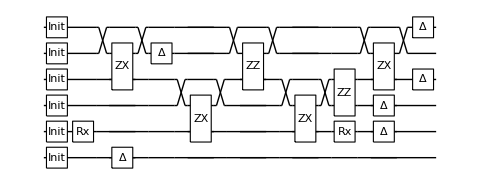

Compilation with automatically generated ansatz at Thu 23 Feb 2023 13:36:11 with grad NGAN

@cycle1:Thu 23 Feb 2023 13:37:50, fev:504, <E>: -0.8472090348494951 nansatz: 7 merged-smallθ-metric-bf-gmerged: {0, 11, 0, 3, 22}

Slowing down @cycle 2

@cycle2:Thu 23 Feb 2023 13:39:45, fev:915, <E>: -0.8472090348494951 nansatz: 7 merged-smallθ-metric-bf-gmerged: {0, 11, 0, 3, 26}

Slowing down @cycle 3

@cycle3:Thu 23 Feb 2023 13:42:55, fev:1482, <E>: -0.8472090348494951 nansatz: 7 merged-smallθ-metric-bf-gmerged: {0, 11, 0, 3, 38}

dist 4. ; runtime 6.74207 min ; ϵ=0.0859623

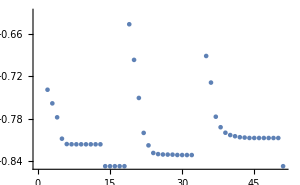

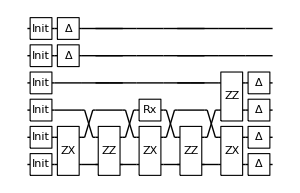

Compilation with automatically generated ansatz at Thu 23 Feb 2023 13:42:55 with grad NGAN

@cycle1:Thu 23 Feb 2023 13:44:47, fev:610, <E>: -0.8472795416493648 nansatz: 6 merged-smallθ-metric-bf-gmerged: {1, 6, 0, 11, 12}

Slowing down @cycle 2

@cycle2:Thu 23 Feb 2023 13:46:33, fev:997, <E>: -0.8472795416493648 nansatz: 6 merged-smallθ-metric-bf-gmerged: {1, 6, 0, 11, 20}

Slowing down @cycle 3

@cycle3:Thu 23 Feb 2023 13:49:13, fev:1448, <E>: -0.8472795416493648 nansatz: 6 merged-smallθ-metric-bf-gmerged: {1, 6, 0, 11, 35}

dist 4.25 ; runtime 6.32752 min ; ϵ=0.0858838

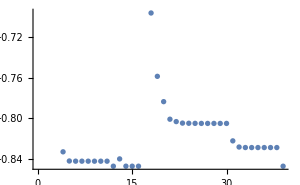

-Graphics-

Compilation with automatically generated ansatz at Thu 23 Feb 2023 13:49:15 with grad NGAN

@cycle1:Thu 23 Feb 2023 13:51:06, fev:596, <E>: -0.4419169754128159 nansatz: 9 merged-smallθ-metric-bf-gmerged: {0, 1, 0, 11, 16}

@cycle2:Thu 23 Feb 2023 13:53:50, fev:1239, <E>: -0.44449123002874985 nansatz: 8 merged-smallθ-metric-bf-gmerged: {0, 15, 0, 23, 25}

@cycle3:Thu 23 Feb 2023 13:55:52, fev:1753, <E>: -0.010033131828222824 nansatz: 0 merged-smallθ-metric-bf-gmerged: {0, 25, 0, 39, 27}

@cycle4:Thu 23 Feb 2023 14:00:57, fev:2674, <E>: -0.5231259227787962 nansatz: 46 merged-smallθ-metric-bf-gmerged: {0, 45, 0, 39, 41}

@cycle5:Thu 23 Feb 2023 14:06:16, fev:3806, <E>: -0.7849259238149393 nansatz: 27 merged-smallθ-metric-bf-gmerged: {0, 52, 0, 83, 46}

Slowing down @cycle 6

@cycle6:Thu 23 Feb 2023 14:08:23, fev:4184, <E>: -0.7849259238149393 nansatz: 27 merged-smallθ-metric-bf-gmerged: {0, 52, 0, 83, 47}

Slowing down @cycle 7

@cycle7:Thu 23 Feb 2023 14:11:06, fev:4644, <E>: -0.7849259238149393 nansatz: 27 merged-smallθ-metric-bf-gmerged: {0, 52, 0, 83, 54}

dist 4.5 ; runtime 22.1177 min ; ϵ=0.148239

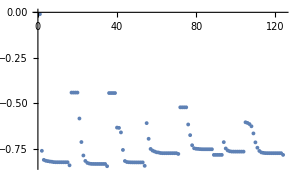

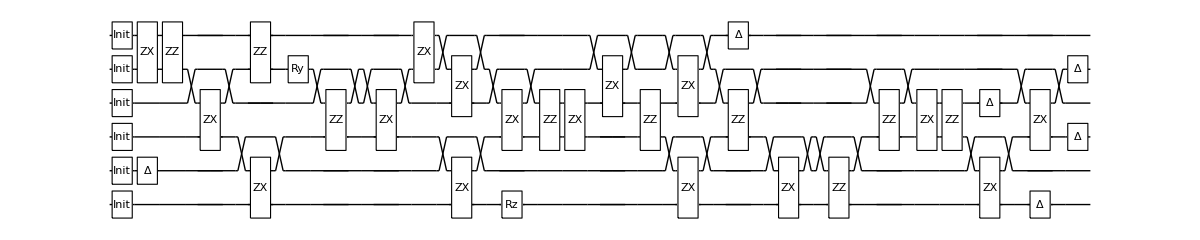

Compilation with automatically generated ansatz at Thu 23 Feb 2023 14:11:22 with grad NGAN

@cycle1:Thu 23 Feb 2023 14:13:05, fev:575, <E>: -0.4982630017224631 nansatz: 2 merged-smallθ-metric-bf-gmerged: {0, 4, 0, 14, 17}

@cycle2:Thu 23 Feb 2023 14:14:56, fev:1107, <E>: -0.5017217183967522 nansatz: 2 merged-smallθ-metric-bf-gmerged: {0, 23, 0, 21, 36}

@cycle3:Thu 23 Feb 2023 14:16:52, fev:1731, <E>: -0.44986645012760584 nansatz: 26 merged-smallθ-metric-bf-gmerged: {0, 28, 0, 21, 38}

@cycle4:Thu 23 Feb 2023 14:19:59, fev:2376, <E>: -0.7586317206547841 nansatz: 37 merged-smallθ-metric-bf-gmerged: {0, 46, 0, 30, 47}

Slowing down @cycle 5

@cycle5:Thu 23 Feb 2023 14:22:03, fev:2727, <E>: -0.7586317206547841 nansatz: 37 merged-smallθ-metric-bf-gmerged: {0, 46, 0, 30, 49}

Slowing down @cycle 6

@cycle6:Thu 23 Feb 2023 14:25:08, fev:3204, <E>: -0.7586317206547841 nansatz: 37 merged-smallθ-metric-bf-gmerged: {0, 46, 0, 30, 53}

dist 4.75 ; runtime 13.7684 min ; ϵ=0.174532

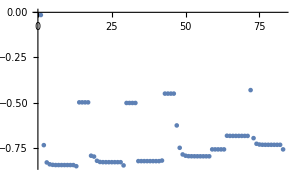

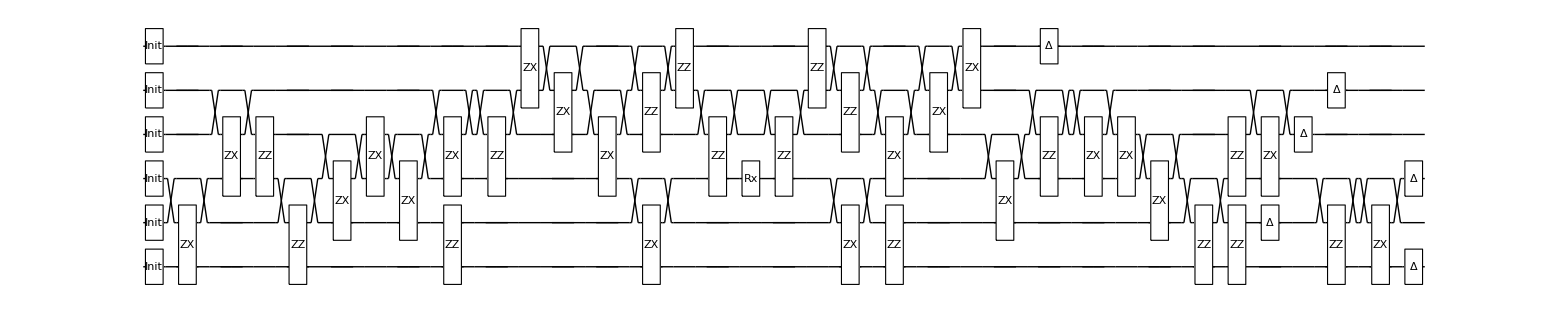

Compilation with automatically generated ansatz at Thu 23 Feb 2023 14:25:08 with grad NGAN

@cycle1:Thu 23 Feb 2023 14:26:55, fev:673, <E>: -0.5915512266198789 nansatz: 11 merged-smallθ-metric-bf-gmerged: {0, 2, 0, 15, 16}

@cycle2:Thu 23 Feb 2023 14:29:35, fev:1351, <E>: -0.8516873368917187 nansatz: 2 merged-smallθ-metric-bf-gmerged: {0, 13, 0, 45, 22}

Slowing down @cycle 3

@cycle3:Thu 23 Feb 2023 14:30:33, fev:1689, <E>: -0.8516873368917187 nansatz: 2 merged-smallθ-metric-bf-gmerged: {0, 13, 0, 45, 29}

Slowing down @cycle 4

@cycle4:Thu 23 Feb 2023 14:31:58, fev:2170, <E>: -0.8516873368917187 nansatz: 2 merged-smallθ-metric-bf-gmerged: {0, 13, 0, 45, 44}

dist 5. ; runtime 6.83161 min ; ϵ=0.0814764

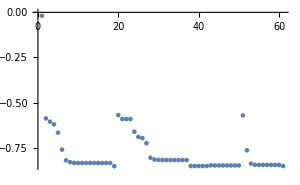

-Graphics-

{Null,Null,Null,Null,Null,Null,Null}

```mathematica
Table[
 {distance, hamfile, hamiltonian, groundstate} = Values@data;
 dev = SuperconductingHub[];
 conf = DefaultConfig[dev, hamiltonian];
 conf["groundstate"] = groundstate;
    res = VQEonVQD[conf];
 {runtime, cost, Elist, ansatz, θvars, finmsg, ncycle, fev, aborted, cycleres, elimmerge, elimbfsmall, elimmetov, elimbf} = res;
 AppendTo[H2onSQC0, <|"runtime" -> runtime, "ansatz" -> ansatz, "θvars" -> θvars, "groundstate" -> groundstate, "cost" -> cost, "fev" -> fev|>];
 DumpSave["H2onSQC0.mx", H2onSQC0];
 Print["dist ", distance, " ; runtime ", runtime, " ; ϵ=", Last@Elist - conf["groundstate"]];
 Print[ListPlot[Elist, ImageSize -> 300]];
 Print[DrawCircuit[ansatz, 6]];
 , {data, gsH2[[37;;]]}]
```

### (1) Expressive 2-qubit gates : H2onSQC1.mx

Compilation with automatically generated ansatz at Tue 21 Feb 2023 23:59:25 with grad NGAN

@cycle1:Wed 22 Feb 2023 00:01:43, fev:521, <E>: -0.5729987460153108 nansatz: 2 merged-smallθ-metric-bf-gmerged: {2, 18, 0, 3, 30}

Slowing down @cycle 2

@cycle2:Wed 22 Feb 2023 00:03:16, fev:785, <E>: -0.5729987460153108 nansatz: 2 merged-smallθ-metric-bf-gmerged: {2, 18, 0, 3, 64}

Slowing down @cycle 3

@cycle3:Wed 22 Feb 2023 00:05:27, fev:1128, <E>: -0.5729987460153108 nansatz: 2 merged-smallθ-metric-bf-gmerged: {2, 18, 0, 3, 99}

dist 0.35 ; runtime 6.11859 min ; ϵ=0.216271

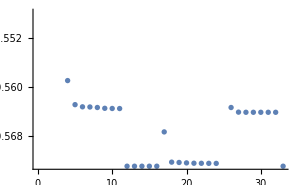

-Graphics-

Compilation with automatically generated ansatz at Wed 22 Feb 2023 00:05:32 with grad NGAN

@cycle1:Wed 22 Feb 2023 00:07:45, fev:582, <E>: -0.684393263500636 nansatz: 6 merged-smallθ-metric-bf-gmerged: {0, 16, 0, 1, 28}

Slowing down @cycle 2

@cycle2:Wed 22 Feb 2023 00:09:40, fev:880, <E>: -0.684393263500636 nansatz: 6 merged-smallθ-metric-bf-gmerged: {0, 16, 0, 1, 51}

@cycle3:Wed 22 Feb 2023 00:12:53, fev:1475, <E>: -0.6845071367809707 nansatz: 12 merged-smallθ-metric-bf-gmerged: {2, 34, 0, 6, 88}

Slowing down @cycle 4

@cycle4:Wed 22 Feb 2023 00:16:26, fev:1855, <E>: -0.6845071367809707 nansatz: 12 merged-smallθ-metric-bf-gmerged: {2, 34, 0, 6, 117}

Slowing down @cycle 5

@cycle5:Wed 22 Feb 2023 00:21:49, fev:2324, <E>: -0.6845071367809707 nansatz: 12 merged-smallθ-metric-bf-gmerged: {2, 34, 0, 6, 166}

dist 0.39 ; runtime 16.4722 min ; ϵ=0.208455

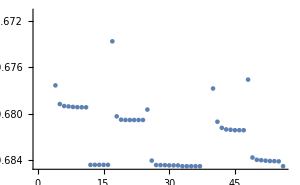

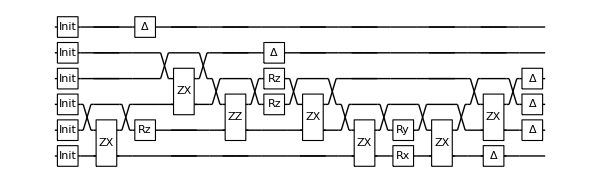

Compilation with automatically generated ansatz at Wed 22 Feb 2023 00:22:01 with grad NGAN

@cycle1:Wed 22 Feb 2023 00:24:29, fev:569, <E>: -0.7679603024438543 nansatz: 2 merged-smallθ-metric-bf-gmerged: {0, 22, 0, 3, 25}

Slowing down @cycle 2

@cycle2:Wed 22 Feb 2023 00:25:56, fev:837, <E>: -0.7679603024438543 nansatz: 2 merged-smallθ-metric-bf-gmerged: {0, 22, 0, 3, 58}

Slowing down @cycle 3

@cycle3:Wed 22 Feb 2023 00:28:17, fev:1180, <E>: -0.7679603024438543 nansatz: 2 merged-smallθ-metric-bf-gmerged: {0, 22, 0, 3, 96}

dist 0.43 ; runtime 6.28335 min ; ϵ=0.200646

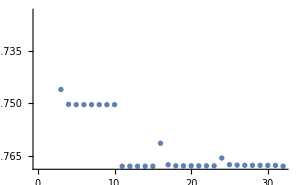

-Graphics-

Compilation with automatically generated ansatz at Wed 22 Feb 2023 00:28:18 with grad NGAN

@cycle1:Wed 22 Feb 2023 00:30:45, fev:597, <E>: -0.8303724530403438 nansatz: 2 merged-smallθ-metric-bf-gmerged: {2, 5, 0, 15, 32}

Slowing down @cycle 2

@cycle2:Wed 22 Feb 2023 00:32:11, fev:861, <E>: -0.8303724530403438 nansatz: 2 merged-smallθ-metric-bf-gmerged: {2, 5, 0, 15, 53}

Slowing down @cycle 3

@cycle3:Wed 22 Feb 2023 00:34:32, fev:1198, <E>: -0.8303724530403438 nansatz: 2 merged-smallθ-metric-bf-gmerged: {2, 5, 0, 15, 91}

dist 0.47 ; runtime 6.23831 min ; ϵ=0.193501

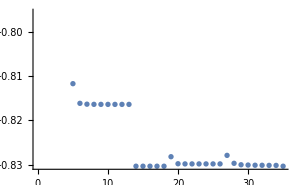

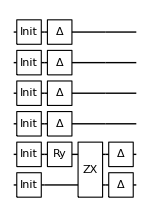

Compilation with automatically generated ansatz at Wed 22 Feb 2023 00:34:32 with grad NGAN

@cycle1:Wed 22 Feb 2023 00:37:03, fev:615, <E>: -0.8770801181688344 nansatz: 9 merged-smallθ-metric-bf-gmerged: {0, 19, 0, 0, 26}

Slowing down @cycle 2

@cycle2:Wed 22 Feb 2023 00:39:12, fev:921, <E>: -0.8770801181688344 nansatz: 9 merged-smallθ-metric-bf-gmerged: {0, 19, 0, 0, 57}

Slowing down @cycle 3

@cycle3:Wed 22 Feb 2023 00:42:27, fev:1271, <E>: -0.8770801181688344 nansatz: 9 merged-smallθ-metric-bf-gmerged: {0, 19, 0, 0, 87}

dist 0.51 ; runtime 8.05165 min ; ϵ=0.18691

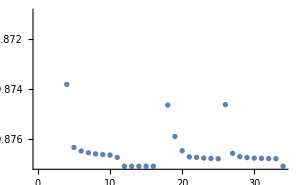

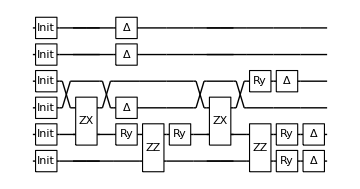

Compilation with automatically generated ansatz at Wed 22 Feb 2023 00:42:35 with grad NGAN

@cycle1:Wed 22 Feb 2023 00:45:00, fev:667, <E>: -0.9118556435027343 nansatz: 7 merged-smallθ-metric-bf-gmerged: {2, 9, 0, 5, 28}

Slowing down @cycle 2

@cycle2:Wed 22 Feb 2023 00:46:46, fev:934, <E>: -0.9118556435027343 nansatz: 7 merged-smallθ-metric-bf-gmerged: {2, 9, 0, 5, 53}

Slowing down @cycle 3

@cycle3:Wed 22 Feb 2023 00:49:27, fev:1277, <E>: -0.9118556435027343 nansatz: 7 merged-smallθ-metric-bf-gmerged: {2, 9, 0, 5, 86}

dist 0.55 ; runtime 6.92754 min ; ϵ=0.180774

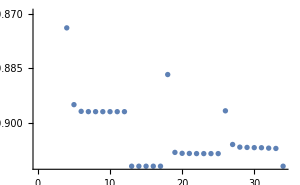

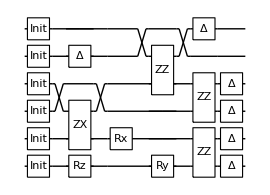

Compilation with automatically generated ansatz at Wed 22 Feb 2023 00:49:31 with grad NGAN

@cycle1:Wed 22 Feb 2023 00:52:01, fev:615, <E>: -0.9373802638044895 nansatz: 2 merged-smallθ-metric-bf-gmerged: {1, 4, 6, 10, 26}

Slowing down @cycle 2

@cycle2:Wed 22 Feb 2023 00:53:32, fev:884, <E>: -0.9373802638044895 nansatz: 2 merged-smallθ-metric-bf-gmerged: {1, 4, 6, 10, 52}

Slowing down @cycle 3

@cycle3:Wed 22 Feb 2023 00:55:44, fev:1217, <E>: -0.9373802638044895 nansatz: 2 merged-smallθ-metric-bf-gmerged: {1, 4, 6, 10, 91}

dist 0.59 ; runtime 6.21411 min ; ϵ=0.17508

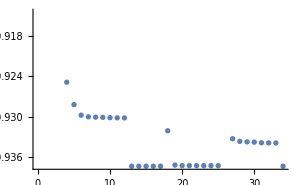

-Graphics-

Compilation with automatically generated ansatz at Wed 22 Feb 2023 00:55:44 with grad NGAN

@cycle1:Wed 22 Feb 2023 00:58:04, fev:616, <E>: -0.9555190583825541 nansatz: 2 merged-smallθ-metric-bf-gmerged: {2, 16, 0, 5, 28}

Slowing down @cycle 2

@cycle2:Wed 22 Feb 2023 00:59:32, fev:876, <E>: -0.9555190583825541 nansatz: 2 merged-smallθ-metric-bf-gmerged: {2, 16, 0, 5, 47}

Slowing down @cycle 3

@cycle3:Wed 22 Feb 2023 01:01:54, fev:1211, <E>: -0.9555190583825541 nansatz: 2 merged-smallθ-metric-bf-gmerged: {2, 16, 0, 5, 76}

dist 0.63 ; runtime 6.16364 min ; ϵ=0.169951

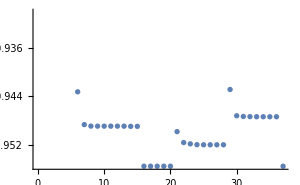

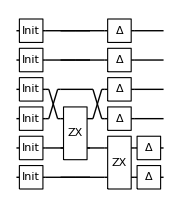

Compilation with automatically generated ansatz at Wed 22 Feb 2023 01:01:54 with grad NGAN

@cycle1:Wed 22 Feb 2023 01:04:25, fev:609, <E>: -0.9678500538583824 nansatz: 10 merged-smallθ-metric-bf-gmerged: {1, 12, 0, 3, 22}

Slowing down @cycle 2

@cycle2:Wed 22 Feb 2023 01:06:31, fev:886, <E>: -0.9678500538583824 nansatz: 10 merged-smallθ-metric-bf-gmerged: {1, 12, 0, 3, 49}

Slowing down @cycle 3

@cycle3:Wed 22 Feb 2023 01:09:40, fev:1260, <E>: -0.9678500538583824 nansatz: 10 merged-smallθ-metric-bf-gmerged: {1, 12, 0, 3, 78}

dist 0.67 ; runtime 7.88915 min ; ϵ=0.165324

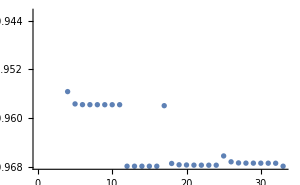

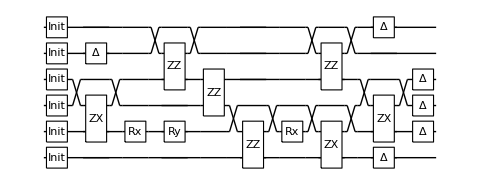

Compilation with automatically generated ansatz at Wed 22 Feb 2023 01:09:47 with grad NGAN

@cycle1:Wed 22 Feb 2023 01:12:35, fev:716, <E>: -0.9755939362728709 nansatz: 8 merged-smallθ-metric-bf-gmerged: {0, 8, 0, 13, 23}

Slowing down @cycle 2

@cycle2:Wed 22 Feb 2023 01:14:30, fev:978, <E>: -0.9755939362728709 nansatz: 8 merged-smallθ-metric-bf-gmerged: {0, 8, 0, 13, 47}

Slowing down @cycle 3

@cycle3:Wed 22 Feb 2023 01:17:15, fev:1312, <E>: -0.9755939362728709 nansatz: 8 merged-smallθ-metric-bf-gmerged: {0, 8, 0, 13, 83}

dist 0.71 ; runtime 7.53796 min ; ϵ=0.161156

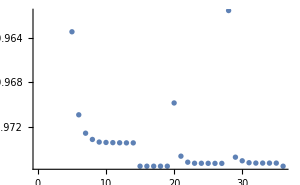

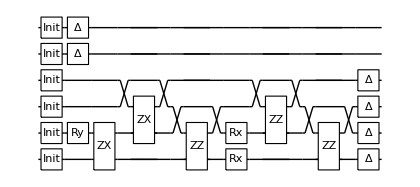

Compilation with automatically generated ansatz at Wed 22 Feb 2023 01:17:20 with grad NGAN

@cycle1:Wed 22 Feb 2023 01:19:29, fev:556, <E>: -0.9796595431322447 nansatz: 2 merged-smallθ-metric-bf-gmerged: {1, 24, 0, 1, 30}

Slowing down @cycle 2

@cycle2:Wed 22 Feb 2023 01:21:01, fev:819, <E>: -0.9796595431322447 nansatz: 2 merged-smallθ-metric-bf-gmerged: {1, 24, 0, 1, 47}

Slowing down @cycle 3

@cycle3:Wed 22 Feb 2023 01:23:21, fev:1154, <E>: -0.9796595431322447 nansatz: 2 merged-smallθ-metric-bf-gmerged: {1, 24, 0, 1, 82}

dist 0.75 ; runtime 6.02666 min ; ϵ=0.157458

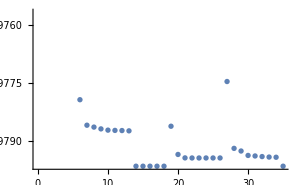

-Graphics-

Compilation with automatically generated ansatz at Wed 22 Feb 2023 01:23:22 with grad NGAN

@cycle1:Wed 22 Feb 2023 01:25:56, fev:631, <E>: -0.9807889119949265 nansatz: 2 merged-smallθ-metric-bf-gmerged: {1, 21, 0, 5, 24}

Slowing down @cycle 2

@cycle2:Wed 22 Feb 2023 01:27:27, fev:891, <E>: -0.9807889119949265 nansatz: 2 merged-smallθ-metric-bf-gmerged: {1, 21, 0, 5, 59}

Slowing down @cycle 3

@cycle3:Wed 22 Feb 2023 01:29:44, fev:1226, <E>: -0.9807889119949265 nansatz: 2 merged-smallθ-metric-bf-gmerged: {1, 21, 0, 5, 94}

dist 0.79 ; runtime 6.38293 min ; ϵ=0.154208

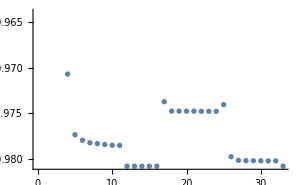

-Graphics-

Compilation with automatically generated ansatz at Wed 22 Feb 2023 01:29:45 with grad NGAN

@cycle1:Wed 22 Feb 2023 01:32:16, fev:681, <E>: -0.979568629702349 nansatz: 6 merged-smallθ-metric-bf-gmerged: {0, 13, 0, 10, 29}

Slowing down @cycle 2

@cycle2:Wed 22 Feb 2023 01:34:01, fev:941, <E>: -0.979568629702349 nansatz: 6 merged-smallθ-metric-bf-gmerged: {0, 13, 0, 10, 49}

Slowing down @cycle 3

@cycle3:Wed 22 Feb 2023 01:36:38, fev:1282, <E>: -0.979568629702349 nansatz: 6 merged-smallθ-metric-bf-gmerged: {0, 13, 0, 10, 78}

dist 0.83 ; runtime 6.9688 min ; ϵ=0.151389

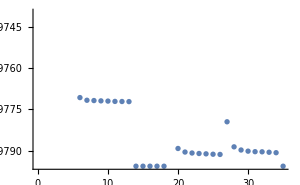

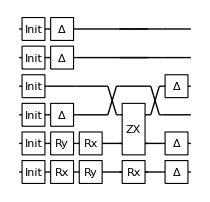

Compilation with automatically generated ansatz at Wed 22 Feb 2023 01:36:43 with grad NGAN

@cycle1:Wed 22 Feb 2023 01:39:17, fev:615, <E>: -0.9758490236040552 nansatz: 6 merged-smallθ-metric-bf-gmerged: {0, 17, 0, 4, 24}

Slowing down @cycle 2

@cycle2:Wed 22 Feb 2023 01:41:05, fev:896, <E>: -0.9758490236040552 nansatz: 6 merged-smallθ-metric-bf-gmerged: {0, 17, 0, 4, 51}

Slowing down @cycle 3

@cycle3:Wed 22 Feb 2023 01:44:03, fev:1271, <E>: -0.9758490236040552 nansatz: 6 merged-smallθ-metric-bf-gmerged: {0, 17, 0, 4, 81}

dist 0.87 ; runtime 7.39039 min ; ϵ=0.149597

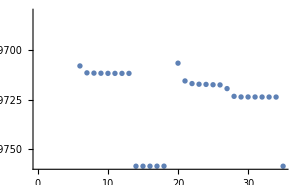

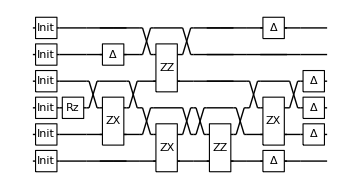

Compilation with automatically generated ansatz at Wed 22 Feb 2023 01:44:06 with grad NGAN

@cycle1:Wed 22 Feb 2023 01:46:51, fev:679, <E>: -0.9717946942704264 nansatz: 8 merged-smallθ-metric-bf-gmerged: {1, 12, 0, 6, 36}

Slowing down @cycle 2

@cycle2:Wed 22 Feb 2023 01:48:40, fev:954, <E>: -0.9717946942704264 nansatz: 8 merged-smallθ-metric-bf-gmerged: {1, 12, 0, 6, 67}

Slowing down @cycle 3

@cycle3:Wed 22 Feb 2023 01:51:47, fev:1322, <E>: -0.9717946942704264 nansatz: 8 merged-smallθ-metric-bf-gmerged: {1, 12, 0, 6, 99}

dist 0.91 ; runtime 7.78498 min ; ϵ=0.147019

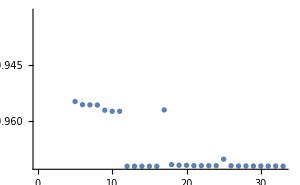

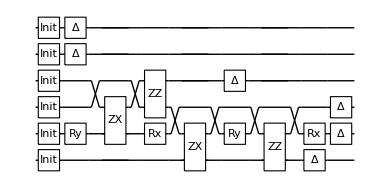

Compilation with automatically generated ansatz at Wed 22 Feb 2023 01:51:53 with grad NGAN

@cycle1:Wed 22 Feb 2023 01:54:31, fev:577, <E>: -0.9659634711667432 nansatz: 2 merged-smallθ-metric-bf-gmerged: {0, 6, 4, 9, 32}

Slowing down @cycle 2

@cycle2:Wed 22 Feb 2023 01:55:56, fev:837, <E>: -0.9659634711667432 nansatz: 2 merged-smallθ-metric-bf-gmerged: {0, 6, 4, 9, 63}

Slowing down @cycle 3

@cycle3:Wed 22 Feb 2023 01:58:09, fev:1167, <E>: -0.9659634711667432 nansatz: 2 merged-smallθ-metric-bf-gmerged: {0, 6, 4, 9, 94}

dist 0.95 ; runtime 6.26203 min ; ϵ=0.145376

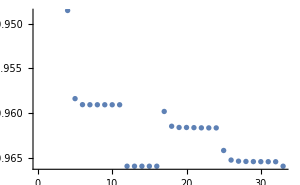

-Graphics-

Compilation with automatically generated ansatz at Wed 22 Feb 2023 01:58:09 with grad NGAN

@cycle1:Wed 22 Feb 2023 02:00:45, fev:660, <E>: -0.958775407799612 nansatz: 2 merged-smallθ-metric-bf-gmerged: {3, 4, 0, 16, 42}

Slowing down @cycle 2

@cycle2:Wed 22 Feb 2023 02:02:13, fev:922, <E>: -0.958775407799612 nansatz: 2 merged-smallθ-metric-bf-gmerged: {3, 4, 0, 16, 74}

Slowing down @cycle 3

@cycle3:Wed 22 Feb 2023 02:04:33, fev:1254, <E>: -0.958775407799612 nansatz: 2 merged-smallθ-metric-bf-gmerged: {3, 4, 0, 16, 107}

dist 0.99 ; runtime 6.40399 min ; ϵ=0.144472

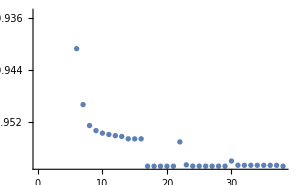

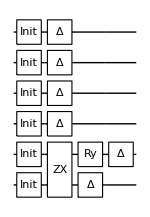

Compilation with automatically generated ansatz at Wed 22 Feb 2023 02:04:34 with grad NGAN

@cycle1:Wed 22 Feb 2023 02:07:07, fev:583, <E>: -0.9572474514090987 nansatz: 2 merged-smallθ-metric-bf-gmerged: {0, 15, 0, 8, 20}

Slowing down @cycle 2

@cycle2:Wed 22 Feb 2023 02:08:34, fev:843, <E>: -0.9572474514090987 nansatz: 2 merged-smallθ-metric-bf-gmerged: {0, 15, 0, 8, 33}

Slowing down @cycle 3

@cycle3:Wed 22 Feb 2023 02:11:09, fev:1178, <E>: -0.9572474514090987 nansatz: 2 merged-smallθ-metric-bf-gmerged: {0, 15, 0, 8, 62}

dist 1. ; runtime 6.58702 min ; ϵ=0.143903

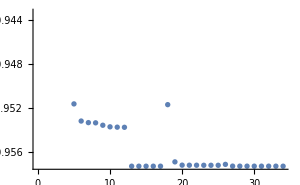

-Graphics-

Compilation with automatically generated ansatz at Wed 22 Feb 2023 02:11:09 with grad NGAN

@cycle1:Wed 22 Feb 2023 02:13:39, fev:614, <E>: -0.936481110623611 nansatz: 2 merged-smallθ-metric-bf-gmerged: {2, 7, 5, 11, 29}

Slowing down @cycle 2

@cycle2:Wed 22 Feb 2023 02:15:06, fev:875, <E>: -0.936481110623611 nansatz: 2 merged-smallθ-metric-bf-gmerged: {2, 7, 5, 11, 57}

Slowing down @cycle 3

@cycle3:Wed 22 Feb 2023 02:17:23, fev:1206, <E>: -0.936481110623611 nansatz: 2 merged-smallθ-metric-bf-gmerged: {2, 7, 5, 11, 81}

dist 1.1 ; runtime 6.23899 min ; ϵ=0.142712

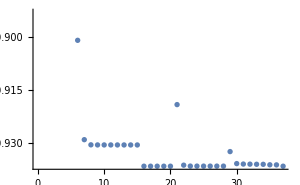

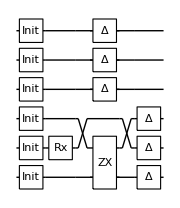

Compilation with automatically generated ansatz at Wed 22 Feb 2023 02:17:23 with grad NGAN

@cycle1:Wed 22 Feb 2023 02:20:16, fev:651, <E>: -0.912918249354794 nansatz: 6 merged-smallθ-metric-bf-gmerged: {0, 14, 0, 4, 28}

Slowing down @cycle 2

@cycle2:Wed 22 Feb 2023 02:22:03, fev:916, <E>: -0.912918249354794 nansatz: 6 merged-smallθ-metric-bf-gmerged: {0, 14, 0, 4, 53}

Slowing down @cycle 3

@cycle3:Wed 22 Feb 2023 02:24:51, fev:1252, <E>: -0.912918249354794 nansatz: 6 merged-smallθ-metric-bf-gmerged: {0, 14, 0, 4, 78}

dist 1.2 ; runtime 7.51198 min ; ϵ=0.143822

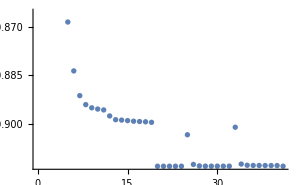

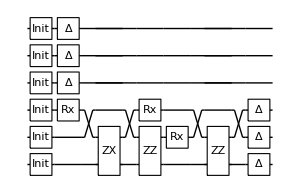

Compilation with automatically generated ansatz at Wed 22 Feb 2023 02:24:54 with grad NGAN

@cycle1:Wed 22 Feb 2023 02:27:27, fev:648, <E>: -0.8879949721888551 nansatz: 2 merged-smallθ-metric-bf-gmerged: {2, 5, 4, 12, 23}

Slowing down @cycle 2

@cycle2:Wed 22 Feb 2023 02:28:59, fev:913, <E>: -0.8879949721888551 nansatz: 2 merged-smallθ-metric-bf-gmerged: {2, 5, 4, 12, 55}

Slowing down @cycle 3

@cycle3:Wed 22 Feb 2023 02:31:18, fev:1245, <E>: -0.8879949721888551 nansatz: 2 merged-smallθ-metric-bf-gmerged: {2, 5, 4, 12, 92}

dist 1.3 ; runtime 6.39919 min ; ϵ=0.147191

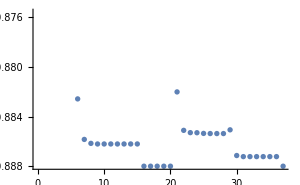

-Graphics-

Compilation with automatically generated ansatz at Wed 22 Feb 2023 02:31:18 with grad NGAN

@cycle1:Wed 22 Feb 2023 02:34:50, fev:899, <E>: -0.8981838880393178 nansatz: 14 merged-smallθ-metric-bf-gmerged: {0, 4, 0, 9, 30}

@cycle2:Wed 22 Feb 2023 02:39:26, fev:1731, <E>: -0.9001350155750851 nansatz: 25 merged-smallθ-metric-bf-gmerged: {2, 11, 0, 15, 59}

Slowing down @cycle 3

@cycle3:Wed 22 Feb 2023 02:42:58, fev:2048, <E>: -0.9001350155750851 nansatz: 25 merged-smallθ-metric-bf-gmerged: {2, 11, 0, 15, 78}

Slowing down @cycle 4

@cycle4:Wed 22 Feb 2023 02:48:31, fev:2455, <E>: -0.9001350155750851 nansatz: 25 merged-smallθ-metric-bf-gmerged: {2, 11, 0, 15, 113}

dist 1.4 ; runtime 18.1442 min ; ϵ=0.115333

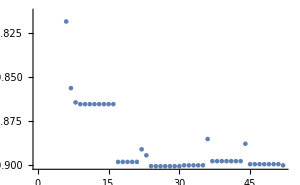

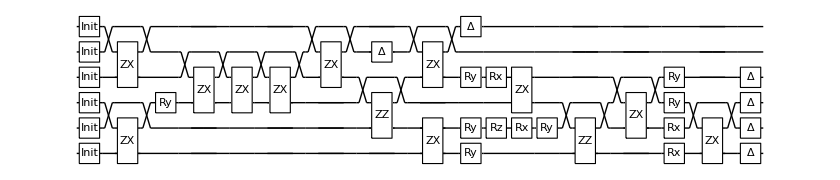

Compilation with automatically generated ansatz at Wed 22 Feb 2023 02:49:27 with grad NGAN

@cycle1:Wed 22 Feb 2023 02:51:53, fev:578, <E>: -0.8378825790948383 nansatz: 2 merged-smallθ-metric-bf-gmerged: {0, 22, 0, 1, 25}

Slowing down @cycle 2

@cycle2:Wed 22 Feb 2023 02:53:29, fev:843, <E>: -0.8378825790948383 nansatz: 2 merged-smallθ-metric-bf-gmerged: {0, 22, 0, 1, 49}

Slowing down @cycle 3

@cycle3:Wed 22 Feb 2023 02:55:58, fev:1181, <E>: -0.8378825790948383 nansatz: 2 merged-smallθ-metric-bf-gmerged: {0, 22, 0, 1, 78}

dist 1.5 ; runtime 6.52291 min ; ϵ=0.160267

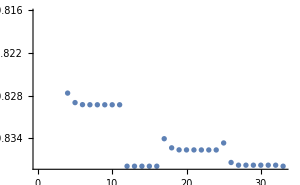

-Graphics-

Compilation with automatically generated ansatz at Wed 22 Feb 2023 02:55:58 with grad NGAN

@cycle1:Wed 22 Feb 2023 02:58:45, fev:678, <E>: -0.8261439863660818 nansatz: 10 merged-smallθ-metric-bf-gmerged: {1, 11, 0, 6, 33}

Slowing down @cycle 2

@cycle2:Wed 22 Feb 2023 03:01:05, fev:982, <E>: -0.8261439863660818 nansatz: 10 merged-smallθ-metric-bf-gmerged: {1, 11, 0, 6, 63}

Slowing down @cycle 3

@cycle3:Wed 22 Feb 2023 03:04:18, fev:1338, <E>: -0.8261439863660818 nansatz: 10 merged-smallθ-metric-bf-gmerged: {1, 11, 0, 6, 91}

dist 1.6 ; runtime 8.47457 min ; ϵ=0.157329

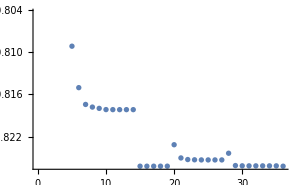

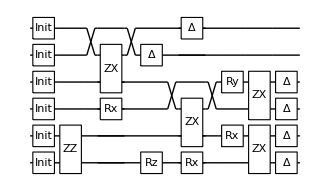

Compilation with automatically generated ansatz at Wed 22 Feb 2023 03:04:27 with grad NGAN

@cycle1:Wed 22 Feb 2023 03:07:21, fev:661, <E>: -0.8294626674032375 nansatz: 2 merged-smallθ-metric-bf-gmerged: {0, 15, 0, 11, 26}

Slowing down @cycle 2

@cycle2:Wed 22 Feb 2023 03:08:48, fev:922, <E>: -0.8294626674032375 nansatz: 2 merged-smallθ-metric-bf-gmerged: {0, 15, 0, 11, 53}

Slowing down @cycle 3

@cycle3:Wed 22 Feb 2023 03:11:00, fev:1253, <E>: -0.8294626674032375 nansatz: 2 merged-smallθ-metric-bf-gmerged: {0, 15, 0, 11, 91}

dist 1.7 ; runtime 6.54852 min ; ϵ=0.141964

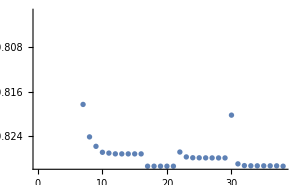

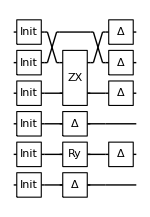

Compilation with automatically generated ansatz at Wed 22 Feb 2023 03:11:00 with grad NGAN

@cycle1:Wed 22 Feb 2023 03:13:56, fev:780, <E>: -0.8359027628573138 nansatz: 10 merged-smallθ-metric-bf-gmerged: {1, 6, 1, 10, 23}

@cycle2:Wed 22 Feb 2023 03:16:12, fev:1269, <E>: -0.837894057018266 nansatz: 8 merged-smallθ-metric-bf-gmerged: {1, 33, 1, 12, 42}

@cycle3:Wed 22 Feb 2023 03:18:59, fev:1834, <E>: -0.8382884892759712 nansatz: 8 merged-smallθ-metric-bf-gmerged: {2, 41, 1, 32, 64}

@cycle4:Wed 22 Feb 2023 03:21:47, fev:2456, <E>: -0.8384271051411984 nansatz: 16 merged-smallθ-metric-bf-gmerged: {2, 48, 1, 46, 81}

Slowing down @cycle 5

@cycle5:Wed 22 Feb 2023 03:24:19, fev:2728, <E>: -0.8384271051411984 nansatz: 16 merged-smallθ-metric-bf-gmerged: {2, 48, 1, 46, 101}

@cycle6:Wed 22 Feb 2023 03:31:24, fev:3753, <E>: -0.8385701590932163 nansatz: 26 merged-smallθ-metric-bf-gmerged: {3, 57, 1, 61, 138}

@cycle7:Wed 22 Feb 2023 03:37:34, fev:4434, <E>: -0.8391475340130923 nansatz: 12 merged-smallθ-metric-bf-gmerged: {5, 98, 1, 65, 169}

@cycle8:Wed 22 Feb 2023 03:41:45, fev:5062, <E>: -0.8396079413984752 nansatz: 13 merged-smallθ-metric-bf-gmerged: {5, 127, 1, 69, 205}

@cycle9:Wed 22 Feb 2023 03:46:56, fev:5794, <E>: -0.8398283016128236 nansatz: 13 merged-smallθ-metric-bf-gmerged: {8, 140, 1, 87, 236}

@cycle10:Wed 22 Feb 2023 03:52:03, fev:6513, <E>: -0.8401130766244527 nansatz: 14 merged-smallθ-metric-bf-gmerged: {11, 164, 1, 95, 267}

@cycle11:Wed 22 Feb 2023 03:58:19, fev:7314, <E>: -0.8402896715593184 nansatz: 22 merged-smallθ-metric-bf-gmerged: {12, 173, 1, 106, 302}

Slowing down @cycle 12

@cycle12:Wed 22 Feb 2023 04:03:27, fev:7664, <E>: -0.8402896715593184 nansatz: 22 merged-smallθ-metric-bf-gmerged: {12, 173, 1, 106, 330}

Slowing down @cycle 13

@cycle13:Wed 22 Feb 2023 04:11:43, fev:8117, <E>: -0.8402896715593184 nansatz: 22 merged-smallθ-metric-bf-gmerged: {12, 173, 1, 106, 376}

dist 1.8 ; runtime 61.5285 min ; ϵ=0.121527

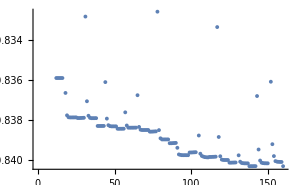

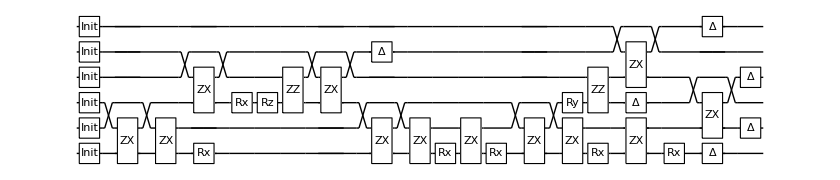

Compilation with automatically generated ansatz at Wed 22 Feb 2023 04:12:32 with grad NGAN

@cycle1:Wed 22 Feb 2023 04:15:28, fev:648, <E>: -0.8405536138837475 nansatz: 6 merged-smallθ-metric-bf-gmerged: {4, 9, 0, 8, 19}

@cycle2:Wed 22 Feb 2023 04:17:52, fev:1110, <E>: -0.8415341295335318 nansatz: 6 merged-smallθ-metric-bf-gmerged: {6, 29, 0, 13, 40}

@cycle3:Wed 22 Feb 2023 04:19:58, fev:1616, <E>: -0.8411545279813135 nansatz: 14 merged-smallθ-metric-bf-gmerged: {7, 48, 0, 13, 62}

@cycle4:Wed 22 Feb 2023 04:22:31, fev:2135, <E>: -0.8431884396067358 nansatz: 10 merged-smallθ-metric-bf-gmerged: {8, 71, 0, 21, 89}

@cycle5:Wed 22 Feb 2023 04:25:22, fev:2640, <E>: -0.8433987279174363 nansatz: 12 merged-smallθ-metric-bf-gmerged: {9, 83, 0, 33, 127}

@cycle6:Wed 22 Feb 2023 04:28:20, fev:3148, <E>: -0.8438034842857645 nansatz: 12 merged-smallθ-metric-bf-gmerged: {10, 99, 0, 42, 156}

@cycle7:Wed 22 Feb 2023 04:31:23, fev:3720, <E>: -0.8443193683949342 nansatz: 12 merged-smallθ-metric-bf-gmerged: {11, 112, 0, 50, 185}

@cycle8:Wed 22 Feb 2023 04:34:38, fev:4237, <E>: -0.8446284539708537 nansatz: 14 merged-smallθ-metric-bf-gmerged: {12, 127, 0, 58, 208}

Slowing down @cycle 9

@cycle9:Wed 22 Feb 2023 04:37:20, fev:4508, <E>: -0.8446284539708537 nansatz: 14 merged-smallθ-metric-bf-gmerged: {12, 127, 0, 58, 235}

Slowing down @cycle 10

@cycle10:Wed 22 Feb 2023 04:41:29, fev:4857, <E>: -0.8446284539708537 nansatz: 14 merged-smallθ-metric-bf-gmerged: {12, 127, 0, 58, 262}

dist 1.9 ; runtime 29.2625 min ; ϵ=0.10971

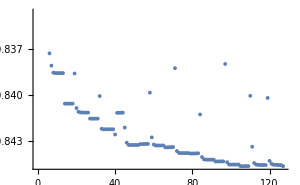

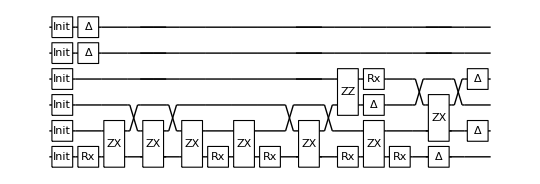

Compilation with automatically generated ansatz at Wed 22 Feb 2023 04:41:48 with grad NGAN

@cycle1:Wed 22 Feb 2023 04:44:33, fev:647, <E>: -0.8439720357888452 nansatz: 2 merged-smallθ-metric-bf-gmerged: {1, 7, 2, 15, 26}

@cycle2:Wed 22 Feb 2023 04:46:18, fev:1106, <E>: -0.8441536235519667 nansatz: 5 merged-smallθ-metric-bf-gmerged: {1, 25, 2, 19, 55}

@cycle3:Wed 22 Feb 2023 04:48:27, fev:1605, <E>: -0.8446801535259224 nansatz: 7 merged-smallθ-metric-bf-gmerged: {2, 42, 2, 26, 84}

@cycle4:Wed 22 Feb 2023 04:50:54, fev:2164, <E>: -0.8449388875622044 nansatz: 11 merged-smallθ-metric-bf-gmerged: {3, 53, 2, 36, 111}

@cycle5:Wed 22 Feb 2023 04:53:57, fev:2730, <E>: -0.8462128131012865 nansatz: 9 merged-smallθ-metric-bf-gmerged: {7, 69, 2, 46, 130}

Slowing down @cycle 6

@cycle6:Wed 22 Feb 2023 04:56:00, fev:2993, <E>: -0.8462128131012865 nansatz: 9 merged-smallθ-metric-bf-gmerged: {7, 69, 2, 46, 154}

@cycle7:Wed 22 Feb 2023 05:00:05, fev:3591, <E>: -0.8470219524903115 nansatz: 10 merged-smallθ-metric-bf-gmerged: {9, 97, 2, 48, 184}

@cycle8:Wed 22 Feb 2023 05:04:50, fev:4183, <E>: -0.8476564530435173 nansatz: 9 merged-smallθ-metric-bf-gmerged: {11, 130, 2, 48, 214}

@cycle9:Wed 22 Feb 2023 05:08:50, fev:4763, <E>: -0.8479382650074763 nansatz: 10 merged-smallθ-metric-bf-gmerged: {11, 158, 2, 49, 249}

@cycle10:Wed 22 Feb 2023 05:13:41, fev:5442, <E>: -0.8480214533544096 nansatz: 12 merged-smallθ-metric-bf-gmerged: {11, 182, 2, 56, 278}

Slowing down @cycle 11

@cycle11:Wed 22 Feb 2023 05:17:23, fev:5784, <E>: -0.8480214533544096 nansatz: 12 merged-smallθ-metric-bf-gmerged: {11, 182, 2, 56, 307}

Slowing down @cycle 12

@cycle12:Wed 22 Feb 2023 05:23:17, fev:6234, <E>: -0.8480214533544096 nansatz: 12 merged-smallθ-metric-bf-gmerged: {11, 182, 2, 56, 361}

dist 2. ; runtime 41.737 min ; ϵ=0.10062

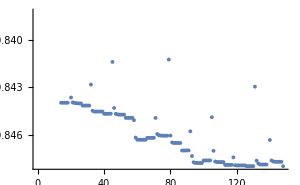

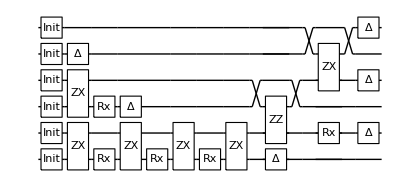

Compilation with automatically generated ansatz at Wed 22 Feb 2023 05:23:32 with grad NGAN

@cycle1:Wed 22 Feb 2023 05:26:15, fev:636, <E>: -0.8464405379933659 nansatz: 2 merged-smallθ-metric-bf-gmerged: {0, 10, 8, 9, 20}

@cycle2:Wed 22 Feb 2023 05:28:11, fev:1101, <E>: -0.8451881020902208 nansatz: 13 merged-smallθ-metric-bf-gmerged: {1, 24, 8, 9, 37}

@cycle3:Wed 22 Feb 2023 05:30:37, fev:1552, <E>: -0.8466310058368518 nansatz: 4 merged-smallθ-metric-bf-gmerged: {1, 57, 8, 9, 66}

@cycle4:Wed 22 Feb 2023 05:33:02, fev:2013, <E>: -0.8466566151443118 nansatz: 9 merged-smallθ-metric-bf-gmerged: {2, 71, 8, 15, 88}

@cycle5:Wed 22 Feb 2023 05:35:57, fev:2545, <E>: -0.8476259911109739 nansatz: 6 merged-smallθ-metric-bf-gmerged: {3, 92, 8, 23, 108}

@cycle6:Wed 22 Feb 2023 05:38:28, fev:3039, <E>: -0.8487197384257719 nansatz: 11 merged-smallθ-metric-bf-gmerged: {3, 115, 8, 24, 128}

@cycle7:Wed 22 Feb 2023 05:41:56, fev:3733, <E>: -0.8495758986642263 nansatz: 14 merged-smallθ-metric-bf-gmerged: {3, 122, 8, 42, 147}

@cycle8:Wed 22 Feb 2023 05:45:31, fev:4370, <E>: -0.8500673038183121 nansatz: 15 merged-smallθ-metric-bf-gmerged: {5, 141, 8, 47, 167}

@cycle9:Wed 22 Feb 2023 05:48:39, fev:4923, <E>: -0.8509898638787362 nansatz: 15 merged-smallθ-metric-bf-gmerged: {6, 162, 8, 52, 191}

@cycle10:Wed 22 Feb 2023 05:52:32, fev:5645, <E>: -0.8512216731355546 nansatz: 21 merged-smallθ-metric-bf-gmerged: {6, 174, 8, 64, 219}

@cycle11:Wed 22 Feb 2023 06:00:03, fev:6745, <E>: -0.8498235511709824 nansatz: 31 merged-smallθ-metric-bf-gmerged: {7, 177, 8, 78, 252}

@cycle12:Wed 22 Feb 2023 06:04:06, fev:7331, <E>: -0.8514517253086961 nansatz: 10 merged-smallθ-metric-bf-gmerged: {9, 212, 8, 82, 299}

Slowing down @cycle 13

@cycle13:Wed 22 Feb 2023 06:06:08, fev:7617, <E>: -0.8514517253086961 nansatz: 10 merged-smallθ-metric-bf-gmerged: {9, 212, 8, 82, 331}

Slowing down @cycle 14

@cycle14:Wed 22 Feb 2023 06:09:14, fev:7977, <E>: -0.8514517253086961 nansatz: 10 merged-smallθ-metric-bf-gmerged: {9, 212, 8, 82, 360}

dist 2.1 ; runtime 45.8535 min ; ϵ=0.092923

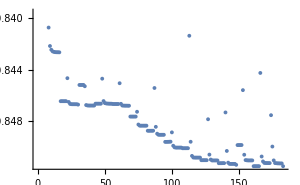

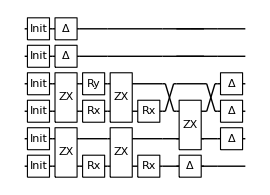

Compilation with automatically generated ansatz at Wed 22 Feb 2023 06:09:23 with grad NGAN

@cycle1:Wed 22 Feb 2023 06:11:42, fev:555, <E>: -0.8482059799552416 nansatz: 2 merged-smallθ-metric-bf-gmerged: {0, 23, 0, 1, 24}

Slowing down @cycle 2

@cycle2:Wed 22 Feb 2023 06:13:12, fev:815, <E>: -0.8482059799552416 nansatz: 2 merged-smallθ-metric-bf-gmerged: {0, 23, 0, 1, 48}

@cycle3:Wed 22 Feb 2023 06:16:03, fev:1362, <E>: -0.8485657705198448 nansatz: 7 merged-smallθ-metric-bf-gmerged: {0, 50, 0, 2, 79}

@cycle4:Wed 22 Feb 2023 06:19:56, fev:2080, <E>: -0.8503014942399343 nansatz: 7 merged-smallθ-metric-bf-gmerged: {3, 65, 0, 17, 104}

@cycle5:Wed 22 Feb 2023 06:23:19, fev:2671, <E>: -0.8507407504319763 nansatz: 9 merged-smallθ-metric-bf-gmerged: {4, 94, 0, 17, 145}

@cycle6:Wed 22 Feb 2023 06:27:15, fev:3278, <E>: -0.8517422697297093 nansatz: 12 merged-smallθ-metric-bf-gmerged: {4, 124, 0, 17, 182}

Slowing down @cycle 7

@cycle7:Wed 22 Feb 2023 06:30:59, fev:3636, <E>: -0.8517422697297093 nansatz: 12 merged-smallθ-metric-bf-gmerged: {4, 124, 0, 17, 216}

Slowing down @cycle 8

@cycle8:Wed 22 Feb 2023 06:37:04, fev:4093, <E>: -0.8517422697297093 nansatz: 12 merged-smallθ-metric-bf-gmerged: {4, 124, 0, 17, 257}

dist 2.2 ; runtime 27.9352 min ; ϵ=0.0894818

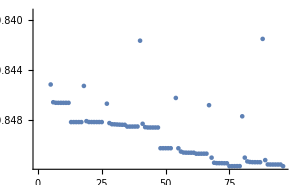

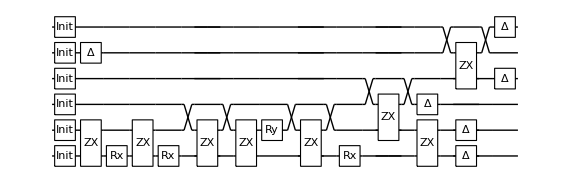

Compilation with automatically generated ansatz at Wed 22 Feb 2023 06:37:20 with grad NGAN

@cycle1:Wed 22 Feb 2023 06:40:09, fev:679, <E>: -0.8507990143405944 nansatz: 9 merged-smallθ-metric-bf-gmerged: {1, 13, 0, 5, 24}

@cycle2:Wed 22 Feb 2023 06:42:52, fev:1184, <E>: -0.8511722466414612 nansatz: 11 merged-smallθ-metric-bf-gmerged: {1, 35, 0, 9, 45}

@cycle3:Wed 22 Feb 2023 06:45:46, fev:1699, <E>: -0.8515293082567479 nansatz: 13 merged-smallθ-metric-bf-gmerged: {1, 57, 0, 12, 71}

@cycle4:Wed 22 Feb 2023 06:49:58, fev:2463, <E>: -0.851740142883598 nansatz: 24 merged-smallθ-metric-bf-gmerged: {1, 64, 0, 21, 97}

@cycle5:Wed 22 Feb 2023 06:54:59, fev:3140, <E>: -0.8541225015395941 nansatz: 14 merged-smallθ-metric-bf-gmerged: {5, 84, 0, 34, 118}

Slowing down @cycle 6

@cycle6:Wed 22 Feb 2023 06:57:19, fev:3424, <E>: -0.8541225015395941 nansatz: 14 merged-smallθ-metric-bf-gmerged: {5, 84, 0, 34, 143}

@cycle7:Wed 22 Feb 2023 07:02:19, fev:4097, <E>: -0.8542428928194101 nansatz: 17 merged-smallθ-metric-bf-gmerged: {7, 106, 0, 41, 164}

Slowing down @cycle 8

@cycle8:Wed 22 Feb 2023 07:06:19, fev:4463, <E>: -0.8542428928194101 nansatz: 17 merged-smallθ-metric-bf-gmerged: {7, 106, 0, 41, 196}

Slowing down @cycle 9

@cycle9:Wed 22 Feb 2023 07:12:49, fev:4922, <E>: -0.8542428928194101 nansatz: 17 merged-smallθ-metric-bf-gmerged: {7, 106, 0, 41, 245}

dist 2.3 ; runtime 35.8026 min ; ϵ=0.0846795

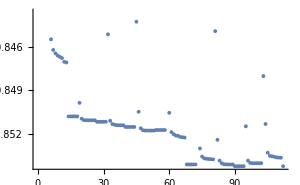

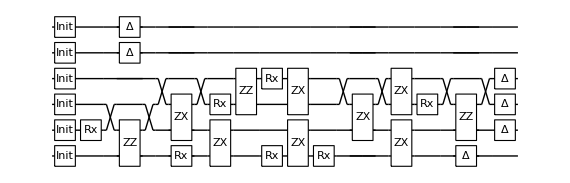

Compilation with automatically generated ansatz at Wed 22 Feb 2023 07:13:08 with grad NGAN

@cycle1:Wed 22 Feb 2023 07:15:33, fev:554, <E>: -0.8449169945315507 nansatz: 2 merged-smallθ-metric-bf-gmerged: {3, 10, 0, 6, 41}

Slowing down @cycle 2

@cycle2:Wed 22 Feb 2023 07:17:04, fev:815, <E>: -0.8449169945315507 nansatz: 2 merged-smallθ-metric-bf-gmerged: {3, 10, 0, 6, 75}

Slowing down @cycle 3

@cycle3:Wed 22 Feb 2023 07:19:26, fev:1148, <E>: -0.8449169945315507 nansatz: 2 merged-smallθ-metric-bf-gmerged: {3, 10, 0, 6, 101}

dist 2.4 ; runtime 6.30206 min ; ϵ=0.092338

-Graphics-

-Graphics-

Compilation with automatically generated ansatz at Wed 22 Feb 2023 07:19:26 with grad NGAN

@cycle1:Wed 22 Feb 2023 07:22:08, fev:686, <E>: -0.8509086388317267 nansatz: 9 merged-smallθ-metric-bf-gmerged: {1, 5, 0, 11, 20}

@cycle2:Wed 22 Feb 2023 07:25:10, fev:1295, <E>: -0.8515012058573352 nansatz: 9 merged-smallθ-metric-bf-gmerged: {2, 20, 0, 20, 43}

@cycle3:Wed 22 Feb 2023 07:28:03, fev:1804, <E>: -0.8517643036733823 nansatz: 11 merged-smallθ-metric-bf-gmerged: {3, 37, 0, 30, 68}

Slowing down @cycle 4

@cycle4:Wed 22 Feb 2023 07:30:28, fev:2070, <E>: -0.8517643036733823 nansatz: 11 merged-smallθ-metric-bf-gmerged: {3, 37, 0, 30, 92}

@cycle5:Wed 22 Feb 2023 07:35:18, fev:2762, <E>: -0.852100134153937 nansatz: 13 merged-smallθ-metric-bf-gmerged: {5, 44, 0, 51, 125}

@cycle6:Wed 22 Feb 2023 07:40:30, fev:3411, <E>: -0.8525647933964517 nansatz: 18 merged-smallθ-metric-bf-gmerged: {6, 53, 0, 66, 153}

Slowing down @cycle 7

@cycle7:Wed 22 Feb 2023 07:45:30, fev:3754, <E>: -0.8525647933964517 nansatz: 18 merged-smallθ-metric-bf-gmerged: {6, 53, 0, 66, 172}

Slowing down @cycle 8

@cycle8:Wed 22 Feb 2023 07:52:24, fev:4183, <E>: -0.8525647933964517 nansatz: 18 merged-smallθ-metric-bf-gmerged: {6, 53, 0, 66, 212}

dist 2.5 ; runtime 33.5428 min ; ϵ=0.0834901

-Graphics-

-Graphics-

Compilation with automatically generated ansatz at Wed 22 Feb 2023 07:52:59 with grad NGAN

@cycle1:Wed 22 Feb 2023 07:55:34, fev:734, <E>: -0.8522751231057705 nansatz: 11 merged-smallθ-metric-bf-gmerged: {1, 12, 0, 5, 27}

@cycle2:Wed 22 Feb 2023 07:58:15, fev:1253, <E>: -0.8527836476319457 nansatz: 15 merged-smallθ-metric-bf-gmerged: {1, 32, 0, 6, 50}

@cycle3:Wed 22 Feb 2023 08:01:41, fev:1826, <E>: -0.8529911506861317 nansatz: 16 merged-smallθ-metric-bf-gmerged: {3, 47, 0, 13, 78}

@cycle4:Wed 22 Feb 2023 08:05:34, fev:2525, <E>: -0.8531119936146593 nansatz: 21 merged-smallθ-metric-bf-gmerged: {5, 55, 0, 25, 106}

Slowing down @cycle 5

@cycle5:Wed 22 Feb 2023 08:08:14, fev:2799, <E>: -0.8531119936146593 nansatz: 21 merged-smallθ-metric-bf-gmerged: {5, 55, 0, 25, 137}

Slowing down @cycle 6

@cycle6:Wed 22 Feb 2023 08:12:22, fev:3137, <E>: -0.8531119936146593 nansatz: 21 merged-smallθ-metric-bf-gmerged: {5, 55, 0, 25, 179}

dist 2.75 ; runtime 19.8894 min ; ϵ=0.081237

-Graphics-

-Graphics-

Compilation with automatically generated ansatz at Wed 22 Feb 2023 08:12:52 with grad NGAN

@cycle1:Wed 22 Feb 2023 08:15:30, fev:583, <E>: -0.8518915561047848 nansatz: 2 merged-smallθ-metric-bf-gmerged: {0, 15, 2, 8, 33}

Slowing down @cycle 2

@cycle2:Wed 22 Feb 2023 08:16:57, fev:844, <E>: -0.8518915561047848 nansatz: 2 merged-smallθ-metric-bf-gmerged: {0, 15, 2, 8, 65}

Slowing down @cycle 3

@cycle3:Wed 22 Feb 2023 08:19:15, fev:1172, <E>: -0.8518915561047848 nansatz: 2 merged-smallθ-metric-bf-gmerged: {0, 15, 2, 8, 91}

dist 3. ; runtime 6.38397 min ; ϵ=0.0817403

-Graphics-

-Graphics-

Compilation with automatically generated ansatz at Wed 22 Feb 2023 08:19:15 with grad NGAN

@cycle1:Wed 22 Feb 2023 08:22:03, fev:604, <E>: -0.8519048894277177 nansatz: 2 merged-smallθ-metric-bf-gmerged: {1, 24, 0, 2, 25}

@cycle2:Wed 22 Feb 2023 08:23:59, fev:1025, <E>: -0.8524444629469654 nansatz: 6 merged-smallθ-metric-bf-gmerged: {4, 40, 0, 5, 51}

@cycle3:Wed 22 Feb 2023 08:26:48, fev:1609, <E>: -0.8527886166500432 nansatz: 12 merged-smallθ-metric-bf-gmerged: {6, 49, 0, 17, 84}

@cycle4:Wed 22 Feb 2023 08:30:05, fev:2145, <E>: -0.8532091607025079 nansatz: 16 merged-smallθ-metric-bf-gmerged: {6, 58, 0, 30, 106}

@cycle5:Wed 22 Feb 2023 08:34:28, fev:2889, <E>: -0.8538481444492539 nansatz: 15 merged-smallθ-metric-bf-gmerged: {10, 70, 0, 41, 138}

@cycle6:Wed 22 Feb 2023 08:38:53, fev:3601, <E>: -0.8541000116115219 nansatz: 16 merged-smallθ-metric-bf-gmerged: {11, 78, 0, 60, 161}

Slowing down @cycle 7

@cycle7:Wed 22 Feb 2023 08:41:54, fev:3873, <E>: -0.8541000116115219 nansatz: 16 merged-smallθ-metric-bf-gmerged: {11, 78, 0, 60, 175}

Slowing down @cycle 8

@cycle8:Wed 22 Feb 2023 08:45:51, fev:4226, <E>: -0.8541000116115219 nansatz: 16 merged-smallθ-metric-bf-gmerged: {11, 78, 0, 60, 212}

dist 3.25 ; runtime 27.0512 min ; ϵ=0.0792413

-Graphics-

-Graphics-

Compilation with automatically generated ansatz at Wed 22 Feb 2023 08:46:19 with grad NGAN

@cycle1:Wed 22 Feb 2023 08:49:09, fev:644, <E>: -0.8518349424101647 nansatz: 12 merged-smallθ-metric-bf-gmerged: {0, 11, 0, 5, 22}

@cycle2:Wed 22 Feb 2023 08:52:24, fev:1202, <E>: -0.8524750784311234 nansatz: 5 merged-smallθ-metric-bf-gmerged: {3, 21, 0, 25, 50}

@cycle3:Wed 22 Feb 2023 08:54:46, fev:1708, <E>: -0.8525601104124483 nansatz: 15 merged-smallθ-metric-bf-gmerged: {3, 22, 0, 43, 68}

Slowing down @cycle 4

@cycle4:Wed 22 Feb 2023 08:57:03, fev:1971, <E>: -0.8525601104124483 nansatz: 15 merged-smallθ-metric-bf-gmerged: {3, 22, 0, 43, 92}

@cycle5:Wed 22 Feb 2023 09:02:37, fev:2835, <E>: -0.8527366552661837 nansatz: 18 merged-smallθ-metric-bf-gmerged: {4, 30, 0, 61, 129}

@cycle6:Wed 22 Feb 2023 09:08:13, fev:3604, <E>: -0.8531052027351406 nansatz: 18 merged-smallθ-metric-bf-gmerged: {7, 46, 0, 75, 167}

Slowing down @cycle 7

@cycle7:Wed 22 Feb 2023 09:12:16, fev:3941, <E>: -0.8531052027351406 nansatz: 18 merged-smallθ-metric-bf-gmerged: {7, 46, 0, 75, 195}

Slowing down @cycle 8

@cycle8:Wed 22 Feb 2023 09:18:17, fev:4367, <E>: -0.8531052027351406 nansatz: 18 merged-smallθ-metric-bf-gmerged: {7, 46, 0, 75, 223}

dist 3.5 ; runtime 32.4362 min ; ϵ=0.0801232

-Graphics-

-Graphics-

Compilation with automatically generated ansatz at Wed 22 Feb 2023 09:18:45 with grad NGAN

@cycle1:Wed 22 Feb 2023 09:21:23, fev:624, <E>: -0.8534184087899946 nansatz: 5 merged-smallθ-metric-bf-gmerged: {0, 13, 2, 5, 22}

Slowing down @cycle 2

@cycle2:Wed 22 Feb 2023 09:23:13, fev:888, <E>: -0.8534184087899946 nansatz: 5 merged-smallθ-metric-bf-gmerged: {0, 13, 2, 5, 46}

Slowing down @cycle 3

@cycle3:Wed 22 Feb 2023 09:25:48, fev:1228, <E>: -0.8534184087899946 nansatz: 5 merged-smallθ-metric-bf-gmerged: {0, 13, 2, 5, 78}

dist 3.75 ; runtime 7.0965 min ; ϵ=0.079768

-Graphics-

-Graphics-

Compilation with automatically generated ansatz at Wed 22 Feb 2023 09:25:51 with grad NGAN

@cycle1:Wed 22 Feb 2023 09:28:36, fev:604, <E>: -0.8526644345641512 nansatz: 5 merged-smallθ-metric-bf-gmerged: {1, 17, 0, 3, 18}

Slowing down @cycle 2

@cycle2:Wed 22 Feb 2023 09:30:20, fev:869, <E>: -0.8526644345641512 nansatz: 5 merged-smallθ-metric-bf-gmerged: {1, 17, 0, 3, 40}

@cycle3:Wed 22 Feb 2023 09:33:39, fev:1430, <E>: -0.8528529362474815 nansatz: 8 merged-smallθ-metric-bf-gmerged: {1, 44, 0, 6, 74}

Slowing down @cycle 4

@cycle4:Wed 22 Feb 2023 09:36:48, fev:1769, <E>: -0.8528529362474815 nansatz: 8 merged-smallθ-metric-bf-gmerged: {1, 44, 0, 6, 94}

Slowing down @cycle 5

@cycle5:Wed 22 Feb 2023 09:41:23, fev:2185, <E>: -0.8528529362474815 nansatz: 8 merged-smallθ-metric-bf-gmerged: {1, 44, 0, 6, 141}

dist 4. ; runtime 15.6371 min ; ϵ=0.0803184

-Graphics-

-Graphics-

Compilation with automatically generated ansatz at Wed 22 Feb 2023 09:41:29 with grad NGAN

@cycle1:Wed 22 Feb 2023 09:44:05, fev:651, <E>: -0.8517441394958583 nansatz: 5 merged-smallθ-metric-bf-gmerged: {1, 10, 0, 12, 20}

Slowing down @cycle 2

@cycle2:Wed 22 Feb 2023 09:45:51, fev:913, <E>: -0.8517441394958583 nansatz: 5 merged-smallθ-metric-bf-gmerged: {1, 10, 0, 12, 36}

Slowing down @cycle 3

@cycle3:Wed 22 Feb 2023 09:48:37, fev:1244, <E>: -0.8517441394958583 nansatz: 5 merged-smallθ-metric-bf-gmerged: {1, 10, 0, 12, 61}

dist 4.25 ; runtime 7.1797 min ; ϵ=0.081422

-Graphics-

-Graphics-

Compilation with automatically generated ansatz at Wed 22 Feb 2023 09:48:40 with grad NGAN

@cycle1:Wed 22 Feb 2023 09:51:12, fev:623, <E>: -0.8517129534154788 nansatz: 2 merged-smallθ-metric-bf-gmerged: {3, 5, 0, 11, 43}

Slowing down @cycle 2

@cycle2:Wed 22 Feb 2023 09:52:47, fev:883, <E>: -0.8517129534154788 nansatz: 2 merged-smallθ-metric-bf-gmerged: {3, 5, 0, 11, 60}

@cycle3:Wed 22 Feb 2023 09:55:49, fev:1428, <E>: -0.8519639524802447 nansatz: 5 merged-smallθ-metric-bf-gmerged: {3, 22, 0, 27, 87}

Slowing down @cycle 4

@cycle4:Wed 22 Feb 2023 09:58:29, fev:1758, <E>: -0.8519639524802447 nansatz: 5 merged-smallθ-metric-bf-gmerged: {3, 22, 0, 27, 122}

Slowing down @cycle 5

@cycle5:Wed 22 Feb 2023 10:02:51, fev:2173, <E>: -0.8519639524802447 nansatz: 5 merged-smallθ-metric-bf-gmerged: {3, 22, 0, 27, 172}

dist 4.5 ; runtime 14.2571 min ; ϵ=0.0812005

-Graphics-

-Graphics-

Compilation with automatically generated ansatz at Wed 22 Feb 2023 10:02:55 with grad NGAN

@cycle1:Wed 22 Feb 2023 10:05:51, fev:671, <E>: -0.8514961135227465 nansatz: 12 merged-smallθ-metric-bf-gmerged: {0, 16, 0, 1, 20}

@cycle2:Wed 22 Feb 2023 10:08:46, fev:1190, <E>: -0.8520802933583851 nansatz: 13 merged-smallθ-metric-bf-gmerged: {0, 39, 0, 3, 38}

@cycle3:Wed 22 Feb 2023 10:12:15, fev:1749, <E>: -0.8523417925301 nansatz: 15 merged-smallθ-metric-bf-gmerged: {0, 60, 0, 10, 57}

Slowing down @cycle 4

@cycle4:Wed 22 Feb 2023 10:14:25, fev:2010, <E>: -0.8523417925301 nansatz: 15 merged-smallθ-metric-bf-gmerged: {0, 60, 0, 10, 84}

@cycle5:Wed 22 Feb 2023 10:20:40, fev:2940, <E>: -0.852694556618152 nansatz: 19 merged-smallθ-metric-bf-gmerged: {1, 71, 2, 25, 114}

@cycle6:Wed 22 Feb 2023 10:29:48, fev:4046, <E>: -0.852803625573088 nansatz: 30 merged-smallθ-metric-bf-gmerged: {3, 80, 2, 37, 152}

Slowing down @cycle 7

@cycle7:Wed 22 Feb 2023 10:35:13, fev:4393, <E>: -0.852803625573088 nansatz: 30 merged-smallθ-metric-bf-gmerged: {3, 80, 2, 37, 193}

Slowing down @cycle 8

@cycle8:Wed 22 Feb 2023 10:43:20, fev:4832, <E>: -0.852803625573088 nansatz: 30 merged-smallθ-metric-bf-gmerged: {3, 80, 2, 37, 235}

dist 4.75 ; runtime 41.598 min ; ϵ=0.0803603

-Graphics-

-Graphics-

Compilation with automatically generated ansatz at Wed 22 Feb 2023 10:44:32 with grad NGAN

@cycle1:Wed 22 Feb 2023 10:47:15, fev:648, <E>: -0.852074650034268 nansatz: 10 merged-smallθ-metric-bf-gmerged: {0, 17, 0, 1, 24}

@cycle2:Wed 22 Feb 2023 10:49:49, fev:1157, <E>: -0.8523077359887508 nansatz: 11 merged-smallθ-metric-bf-gmerged: {0, 41, 0, 2, 50}

@cycle3:Wed 22 Feb 2023 10:52:44, fev:1680, <E>: -0.8524850968793122 nansatz: 11 merged-smallθ-metric-bf-gmerged: {0, 69, 0, 2, 76}

@cycle4:Wed 22 Feb 2023 10:55:33, fev:2191, <E>: -0.8527571377849094 nansatz: 11 merged-smallθ-metric-bf-gmerged: {0, 95, 0, 2, 101}

@cycle5:Wed 22 Feb 2023 10:58:44, fev:2720, <E>: -0.8529057079763723 nansatz: 14 merged-smallθ-metric-bf-gmerged: {0, 116, 0, 4, 133}

Slowing down @cycle 6

@cycle6:Wed 22 Feb 2023 11:01:07, fev:2993, <E>: -0.8529057079763723 nansatz: 14 merged-smallθ-metric-bf-gmerged: {0, 116, 0, 4, 150}

Slowing down @cycle 7

@cycle7:Wed 22 Feb 2023 11:04:55, fev:3329, <E>: -0.8529057079763723 nansatz: 14 merged-smallθ-metric-bf-gmerged: {0, 116, 0, 4, 193}

dist 5. ; runtime 20.731 min ; ϵ=0.0802581

-Graphics-

-Graphics-

{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null}

```mathematica
Table[
 {distance, hamfile, hamiltonian, groundstate} = Values@data;
 dev = SuperconductingHub[];
 conf = DefaultConfig[dev, hamiltonian];
 conf["groundstate"] = groundstate;
    res = VQEonVQD[conf];
 {runtime, cost, Elist, ansatz, θvars, finmsg, ncycle, fev, aborted, cycleres, elimmerge, elimbfsmall, elimmetov, elimbf} = res;
 AppendTo[H2onSQC1, <|"runtime" -> runtime, "ansatz" -> ansatz, "θvars" -> θvars, "groundstate" -> groundstate, "cost" -> cost, "fev" -> fev|>];
 DumpSave["H2onSQC1.mx", H2onSQC1];
 Print["dist ", distance, " ; runtime ", runtime, " ; ϵ=", Last@Elist - conf["groundstate"]];
 Print[ListPlot[Elist, ImageSize -> 300]];
 Print[DrawCircuit[ansatz, 6]];
 , {data, gsH2}]
```

### (2) Parameterised cross-resonance gate + perfect case : H2onSQC2.mx

```mathematica
H2onSQC2={};
```

```mathematica
Options@SuperconductingHub
```

{qubitsNum→6,T1→<|0→63,1→93,2→109,3→115,4→68,5→125|>,T2→<|0→113,1→149,2→185,3→161,4→122,5→200|>,ExcitedInit→<|0→0.032,1→0.021,2→0.008,3→0.009,4→0.025,5→0.007|>,QubitFreq→<|0→4500,1→4900,2→4700,3→5100,4→4900,5→5300|>,ExchangeCoupling→<|0<->1→4,0<->2→1.5,1<->3→1.5,2<->3→4,2<->4→1.5,3<->5→1.5,4<->5→4|>,Anharmonicity→<|0→296.7,1→298.6,2→297.4,3→298.3,4→297.2,5→299.1|>,FidRead→<|0→0.9,1→0.92,2→0.96,3→0.97,4→0.93,5→0.97|>,DurMeas→5,DurRxRy→0.05,DurZX→0.5,DurZZ→0.5,StdPassiveNoise→True,ZZPassiveNoise→True}

```mathematica
Table[
 {distance, hamfile, hamiltonian, groundstate} = Values@data;
 dev = SuperconductingHub[StdPassiveNoise->False, ZZPassiveNoise->False];
 conf = DefaultConfig[dev, hamiltonian];
 conf["virtualmeas"]={};
 conf["initcirc"]={};
 conf["groundstate"] = groundstate;
    res = VQEonVQD[conf];
 {runtime, cost, Elist, ansatz, θvars, finmsg, ncycle, fev, aborted, cycleres, elimmerge, elimbfsmall, elimmetov, elimbf} = res;
 AppendTo[H2onSQC2, <|"runtime" -> runtime, "ansatz" -> ansatz, "θvars" -> θvars, "groundstate" -> groundstate, "cost" -> cost, "fev" -> fev|>];
 DumpSave["H2onSQC2.mx", H2onSQC2];
 Print["dist ", distance, " ; runtime ", runtime, " ; ϵ=", Last@Elist - conf["groundstate"]];
 Print[ListPlot[Elist, ImageSize -> 300]];
 Print[DrawCircuit[ansatz, 6]];
 , {data, gsH2}]
```

Compilation with automatically generated ansatz at Wed 22 Feb 2023 18:06:11 with grad NGAN

@cycle1:Wed 22 Feb 2023 18:08:33, fev:919, <E>: -0.7879710585652366 nansatz: 17 merged-smallθ-metric-bf-gmerged: {0, 7, 0, 13, 20}

@cycle2:Wed 22 Feb 2023 18:10:48, fev:1611, <E>: -0.7892668119283681 nansatz: 18 merged-smallθ-metric-bf-gmerged: {0, 27, 0, 20, 31}

Slowing down @cycle 3

@cycle3:Wed 22 Feb 2023 18:11:54, fev:1976, <E>: -0.7892668119283681 nansatz: 18 merged-smallθ-metric-bf-gmerged: {0, 27, 0, 20, 42}

Slowing down @cycle 4

@cycle4:Wed 22 Feb 2023 18:13:26, fev:2427, <E>: -0.7892668119283681 nansatz: 18 merged-smallθ-metric-bf-gmerged: {0, 27, 0, 20, 64}

dist 0.35 ; runtime 7.5825 min ; ϵ=2.58048×10^-6

-Graphics-

-Graphics-

Compilation with automatically generated ansatz at Wed 22 Feb 2023 18:13:46 with grad NGAN

@cycle1:Wed 22 Feb 2023 18:15:28, fev:715, <E>: -0.8833739136013615 nansatz: 8 merged-smallθ-metric-bf-gmerged: {3, 5, 0, 12, 36}

@cycle2:Wed 22 Feb 2023 18:16:41, fev:1182, <E>: -0.8833798718842487 nansatz: 2 merged-smallθ-metric-bf-gmerged: {3, 27, 0, 30, 59}

Slowing down @cycle 3

@cycle3:Wed 22 Feb 2023 18:17:32, fev:1461, <E>: -0.8833798718842487 nansatz: 2 merged-smallθ-metric-bf-gmerged: {3, 27, 0, 30, 87}

Slowing down @cycle 4

@cycle4:Wed 22 Feb 2023 18:18:48, fev:1824, <E>: -0.8833798718842487 nansatz: 2 merged-smallθ-metric-bf-gmerged: {3, 27, 0, 30, 113}

dist 0.39 ; runtime 5.03676 min ; ϵ=0.00958251

-Graphics-

-Graphics-

Compilation with automatically generated ansatz at Wed 22 Feb 2023 18:18:49 with grad NGAN

@cycle1:Wed 22 Feb 2023 18:20:44, fev:782, <E>: -0.9580128006969836 nansatz: 12 merged-smallθ-metric-bf-gmerged: {0, 8, 0, 15, 26}

@cycle2:Wed 22 Feb 2023 18:22:37, fev:1447, <E>: -0.9686055527694324 nansatz: 14 merged-smallθ-metric-bf-gmerged: {0, 34, 0, 21, 52}

Slowing down @cycle 3

@cycle3:Wed 22 Feb 2023 18:23:25, fev:1773, <E>: -0.9686055527694324 nansatz: 14 merged-smallθ-metric-bf-gmerged: {0, 34, 0, 21, 57}

Slowing down @cycle 4

@cycle4:Wed 22 Feb 2023 18:24:42, fev:2236, <E>: -0.9686055527694324 nansatz: 14 merged-smallθ-metric-bf-gmerged: {0, 34, 0, 21, 77}

dist 0.43 ; runtime 6.02387 min ; ϵ=2.50823×10^-7

-Graphics-

-Graphics-

Compilation with automatically generated ansatz at Wed 22 Feb 2023 18:24:50 with grad NGAN

@cycle1:Wed 22 Feb 2023 18:26:41, fev:775, <E>: -1.0238736173429095 nansatz: 8 merged-smallθ-metric-bf-gmerged: {1, 14, 0, 10, 26}

Slowing down @cycle 2

@cycle2:Wed 22 Feb 2023 18:28:01, fev:1176, <E>: -1.0238736173429095 nansatz: 8 merged-smallθ-metric-bf-gmerged: {1, 14, 0, 10, 41}

Slowing down @cycle 3

@cycle3:Wed 22 Feb 2023 18:30:05, fev:1703, <E>: -1.0238736173429095 nansatz: 8 merged-smallθ-metric-bf-gmerged: {1, 14, 0, 10, 62}

dist 0.47 ; runtime 5.33098 min ; ϵ=2.29433×10^-8

-Graphics-

-Graphics-

Compilation with automatically generated ansatz at Wed 22 Feb 2023 18:30:10 with grad NGAN

@cycle1:Wed 22 Feb 2023 18:32:16, fev:830, <E>: -1.051698216462991 nansatz: 22 merged-smallθ-metric-bf-gmerged: {0, 7, 0, 3, 40}

@cycle2:Wed 22 Feb 2023 18:34:45, fev:1616, <E>: -1.051590091885205 nansatz: 7 merged-smallθ-metric-bf-gmerged: {0, 39, 0, 18, 61}

@cycle3:Wed 22 Feb 2023 18:36:25, fev:2248, <E>: -1.0639898226240332 nansatz: 11 merged-smallθ-metric-bf-gmerged: {0, 61, 0, 19, 82}

Slowing down @cycle 4

@cycle4:Wed 22 Feb 2023 18:37:15, fev:2572, <E>: -1.0639898226240332 nansatz: 11 merged-smallθ-metric-bf-gmerged: {0, 61, 0, 19, 90}

Slowing down @cycle 5

@cycle5:Wed 22 Feb 2023 18:38:19, fev:2978, <E>: -1.0639898226240332 nansatz: 11 merged-smallθ-metric-bf-gmerged: {0, 61, 0, 19, 113}

dist 0.51 ; runtime 8.30859 min ; ϵ=4.09246×10^-8

-Graphics-

-Graphics-

Compilation with automatically generated ansatz at Wed 22 Feb 2023 18:38:29 with grad NGAN

@cycle1:Wed 22 Feb 2023 18:40:33, fev:864, <E>: -1.0926269782545621 nansatz: 19 merged-smallθ-metric-bf-gmerged: {0, 14, 0, 0, 23}

Slowing down @cycle 2

@cycle2:Wed 22 Feb 2023 18:42:04, fev:1236, <E>: -1.0926269782545621 nansatz: 19 merged-smallθ-metric-bf-gmerged: {0, 14, 0, 0, 34}

Slowing down @cycle 3

@cycle3:Wed 22 Feb 2023 18:44:29, fev:1733, <E>: -1.0926269782545621 nansatz: 19 merged-smallθ-metric-bf-gmerged: {0, 14, 0, 0, 48}

dist 0.55 ; runtime 6.45586 min ; ϵ=7.64866×10^-7

-Graphics-

-Graphics-

Compilation with automatically generated ansatz at Wed 22 Feb 2023 18:44:56 with grad NGAN

@cycle1:Wed 22 Feb 2023 18:47:03, fev:872, <E>: -1.1124563749542786 nansatz: 21 merged-smallθ-metric-bf-gmerged: {0, 14, 0, 0, 33}

Slowing down @cycle 2

@cycle2:Wed 22 Feb 2023 18:48:42, fev:1262, <E>: -1.1124563749542786 nansatz: 21 merged-smallθ-metric-bf-gmerged: {0, 14, 0, 0, 46}

Slowing down @cycle 3

@cycle3:Wed 22 Feb 2023 18:51:25, fev:1793, <E>: -1.1124563749542786 nansatz: 21 merged-smallθ-metric-bf-gmerged: {0, 14, 0, 0, 78}

dist 0.59 ; runtime 6.82253 min ; ϵ=2.56455×10^-7

-Graphics-

-Graphics-

Compilation with automatically generated ansatz at Wed 22 Feb 2023 18:51:46 with grad NGAN

@cycle1:Wed 22 Feb 2023 18:54:00, fev:932, <E>: -1.125469568785598 nansatz: 21 merged-smallθ-metric-bf-gmerged: {0, 12, 0, 3, 26}

Slowing down @cycle 2

@cycle2:Wed 22 Feb 2023 18:55:47, fev:1344, <E>: -1.125469568785598 nansatz: 21 merged-smallθ-metric-bf-gmerged: {0, 12, 0, 3, 47}

Slowing down @cycle 3

@cycle3:Wed 22 Feb 2023 18:58:20, fev:1832, <E>: -1.125469568785598 nansatz: 21 merged-smallθ-metric-bf-gmerged: {0, 12, 0, 3, 76}

dist 0.63 ; runtime 6.99421 min ; ϵ=2.73913×10^-8

-Graphics-

-Graphics-

Compilation with automatically generated ansatz at Wed 22 Feb 2023 18:58:45 with grad NGAN

@cycle1:Wed 22 Feb 2023 19:01:05, fev:928, <E>: -1.1331743833680468 nansatz: 29 merged-smallθ-metric-bf-gmerged: {1, 7, 0, 1, 29}

Slowing down @cycle 2

@cycle2:Wed 22 Feb 2023 19:03:08, fev:1347, <E>: -1.1331743833680468 nansatz: 29 merged-smallθ-metric-bf-gmerged: {1, 7, 0, 1, 44}

Slowing down @cycle 3

@cycle3:Wed 22 Feb 2023 19:06:08, fev:1885, <E>: -1.1331743833680468 nansatz: 29 merged-smallθ-metric-bf-gmerged: {1, 7, 0, 1, 78}

dist 0.67 ; runtime 8.20605 min ; ϵ=5.0572×10^-9

-Graphics-

-Graphics-

Compilation with automatically generated ansatz at Wed 22 Feb 2023 19:06:58 with grad NGAN

@cycle1:Wed 22 Feb 2023 19:08:47, fev:784, <E>: -1.117500775608926 nansatz: 11 merged-smallθ-metric-bf-gmerged: {0, 14, 0, 11, 25}

@cycle2:Wed 22 Feb 2023 19:10:25, fev:1393, <E>: -1.1367502912506773 nansatz: 13 merged-smallθ-metric-bf-gmerged: {0, 40, 0, 18, 43}

Slowing down @cycle 3

@cycle3:Wed 22 Feb 2023 19:11:20, fev:1748, <E>: -1.1367502912506773 nansatz: 13 merged-smallθ-metric-bf-gmerged: {0, 40, 0, 18, 52}

Slowing down @cycle 4

@cycle4:Wed 22 Feb 2023 19:12:31, fev:2177, <E>: -1.1367502912506773 nansatz: 13 merged-smallθ-metric-bf-gmerged: {0, 40, 0, 18, 63}

dist 0.71 ; runtime 5.69573 min ; ϵ=1.06033×10^-7

-Graphics-

-Graphics-

Compilation with automatically generated ansatz at Wed 22 Feb 2023 19:12:40 with grad NGAN

@cycle1:Wed 22 Feb 2023 19:14:42, fev:873, <E>: -1.1371170626291818 nansatz: 16 merged-smallθ-metric-bf-gmerged: {0, 8, 0, 9, 26}

dist 0.75 ; runtime 2.27752 min ; ϵ=4.71655×10^-9

-Graphics-

-Graphics-

Compilation with automatically generated ansatz at Wed 22 Feb 2023 19:14:56 with grad NGAN

@cycle1:Wed 22 Feb 2023 19:17:06, fev:922, <E>: -1.1121831619985119 nansatz: 5 merged-smallθ-metric-bf-gmerged: {0, 11, 0, 17, 24}

@cycle2:Wed 22 Feb 2023 19:18:32, fev:1462, <E>: -1.1349967131232197 nansatz: 8 merged-smallθ-metric-bf-gmerged: {0, 15, 0, 45, 45}

@cycle3:Wed 22 Feb 2023 19:19:40, fev:2004, <E>: -1.1349968550314251 nansatz: 15 merged-smallθ-metric-bf-gmerged: {0, 16, 0, 50, 63}

dist 0.79 ; runtime 4.92923 min ; ϵ=1.7033×10^-9

-Graphics-

-Graphics-

Compilation with automatically generated ansatz at Wed 22 Feb 2023 19:19:52 with grad NGAN

@cycle1:Wed 22 Feb 2023 19:22:00, fev:880, <E>: -0.563121734501059 nansatz: 15 merged-smallθ-metric-bf-gmerged: {1, 14, 0, 3, 10}

@cycle2:Wed 22 Feb 2023 19:24:16, fev:1585, <E>: -1.1061557388947187 nansatz: 2 merged-smallθ-metric-bf-gmerged: {1, 46, 0, 18, 34}

@cycle3:Wed 22 Feb 2023 19:25:04, fev:2027, <E>: -1.1062463100541051 nansatz: 14 merged-smallθ-metric-bf-gmerged: {1, 48, 0, 23, 48}

@cycle4:Wed 22 Feb 2023 19:26:17, fev:2566, <E>: -1.1309575933266587 nansatz: 11 merged-smallθ-metric-bf-gmerged: {1, 65, 0, 26, 60}

Slowing down @cycle 5

@cycle5:Wed 22 Feb 2023 19:27:10, fev:2935, <E>: -1.1309575933266587 nansatz: 11 merged-smallθ-metric-bf-gmerged: {1, 65, 0, 26, 65}

Slowing down @cycle 6

@cycle6:Wed 22 Feb 2023 19:28:19, fev:3377, <E>: -1.1309575933266587 nansatz: 11 merged-smallθ-metric-bf-gmerged: {1, 65, 0, 26, 77}

dist 0.83 ; runtime 8.5637 min ; ϵ=3.14987×10^-8

-Graphics-

-Graphics-

Compilation with automatically generated ansatz at Wed 22 Feb 2023 19:28:26 with grad NGAN

@cycle1:Wed 22 Feb 2023 19:30:44, fev:873, <E>: -1.125445859758546 nansatz: 29 merged-smallθ-metric-bf-gmerged: {0, 5, 0, 6, 25}

dist 0.87 ; runtime 2.73334 min ; ϵ=3.69042×10^-9

-Graphics-

-Graphics-

Compilation with automatically generated ansatz at Wed 22 Feb 2023 19:31:10 with grad NGAN

@cycle1:Wed 22 Feb 2023 19:32:58, fev:773, <E>: -1.0895775368745 nansatz: 4 merged-smallθ-metric-bf-gmerged: {0, 14, 0, 13, 17}

@cycle2:Wed 22 Feb 2023 19:34:28, fev:1387, <E>: -1.0926049319563926 nansatz: 19 merged-smallθ-metric-bf-gmerged: {1, 20, 0, 21, 33}

@cycle3:Wed 22 Feb 2023 19:36:39, fev:2134, <E>: -1.1188133680798393 nansatz: 16 merged-smallθ-metric-bf-gmerged: {1, 40, 0, 33, 49}

Slowing down @cycle 4

@cycle4:Wed 22 Feb 2023 19:37:31, fev:2466, <E>: -1.1188133680798393 nansatz: 16 merged-smallθ-metric-bf-gmerged: {1, 40, 0, 33, 60}

@cycle5:Wed 22 Feb 2023 19:39:39, fev:3296, <E>: -1.1188132191975446 nansatz: 22 merged-smallθ-metric-bf-gmerged: {1, 45, 0, 42, 76}

@cycle6:Wed 22 Feb 2023 19:42:02, fev:4122, <E>: -1.11881336453143 nansatz: 27 merged-smallθ-metric-bf-gmerged: {1, 47, 0, 58, 88}

Slowing down @cycle 7

@cycle7:Wed 22 Feb 2023 19:43:57, fev:4598, <E>: -1.11881336453143 nansatz: 27 merged-smallθ-metric-bf-gmerged: {1, 47, 0, 58, 108}

Slowing down @cycle 8

@cycle8:Wed 22 Feb 2023 19:46:39, fev:5165, <E>: -1.11881336453143 nansatz: 27 merged-smallθ-metric-bf-gmerged: {1, 47, 0, 58, 125}

dist 0.91 ; runtime 16.0013 min ; ϵ=7.46728×10^-8

-Graphics-

-Graphics-

Compilation with automatically generated ansatz at Wed 22 Feb 2023 19:47:10 with grad NGAN

@cycle1:Wed 22 Feb 2023 19:48:58, fev:758, <E>: -1.07963692768201 nansatz: 2 merged-smallθ-metric-bf-gmerged: {1, 11, 0, 15, 38}

@cycle2:Wed 22 Feb 2023 19:50:15, fev:1209, <E>: -1.0796369251212825 nansatz: 36 merged-smallθ-metric-bf-gmerged: {1, 11, 0, 15, 59}

@cycle3:Wed 22 Feb 2023 19:53:09, fev:1847, <E>: -1.1113394097535383 nansatz: 11 merged-smallθ-metric-bf-gmerged: {1, 58, 0, 25, 76}

dist 0.95 ; runtime 6.09585 min ; ϵ=7.98261×10^-9

-Graphics-

-Graphics-

Compilation with automatically generated ansatz at Wed 22 Feb 2023 19:53:16 with grad NGAN

@cycle1:Wed 22 Feb 2023 19:55:21, fev:879, <E>: -1.1032476468631542 nansatz: 18 merged-smallθ-metric-bf-gmerged: {1, 7, 0, 5, 25}

Slowing down @cycle 2

@cycle2:Wed 22 Feb 2023 19:57:07, fev:1299, <E>: -1.1032476468631542 nansatz: 18 merged-smallθ-metric-bf-gmerged: {1, 7, 0, 5, 45}

Slowing down @cycle 3

@cycle3:Wed 22 Feb 2023 19:59:52, fev:1837, <E>: -1.1032476468631542 nansatz: 18 merged-smallθ-metric-bf-gmerged: {1, 7, 0, 5, 76}

dist 0.99 ; runtime 6.93544 min ; ϵ=1.43613×10^-8

-Graphics-

-Graphics-

Compilation with automatically generated ansatz at Wed 22 Feb 2023 20:00:13 with grad NGAN

@cycle1:Wed 22 Feb 2023 20:02:25, fev:857, <E>: -1.1011503073267268 nansatz: 22 merged-smallθ-metric-bf-gmerged: {0, 9, 0, 4, 40}

Slowing down @cycle 2

@cycle2:Wed 22 Feb 2023 20:04:16, fev:1262, <E>: -1.1011503073267268 nansatz: 22 merged-smallθ-metric-bf-gmerged: {0, 9, 0, 4, 60}

Slowing down @cycle 3

@cycle3:Wed 22 Feb 2023 20:07:01, fev:1788, <E>: -1.1011503073267268 nansatz: 22 merged-smallθ-metric-bf-gmerged: {0, 9, 0, 4, 80}

dist 1. ; runtime 7.1501 min ; ϵ=2.29059×10^-8

-Graphics-

-Graphics-

Compilation with automatically generated ansatz at Wed 22 Feb 2023 20:07:22 with grad NGAN

@cycle1:Wed 22 Feb 2023 20:09:41, fev:883, <E>: -1.0791929243798555 nansatz: 22 merged-smallθ-metric-bf-gmerged: {0, 6, 0, 3, 23}

Slowing down @cycle 2

@cycle2:Wed 22 Feb 2023 20:11:33, fev:1287, <E>: -1.0791929243798555 nansatz: 22 merged-smallθ-metric-bf-gmerged: {0, 6, 0, 3, 45}

Slowing down @cycle 3

@cycle3:Wed 22 Feb 2023 20:14:17, fev:1806, <E>: -1.0791929243798555 nansatz: 22 merged-smallθ-metric-bf-gmerged: {0, 6, 0, 3, 78}

dist 1.1 ; runtime 7.31388 min ; ϵ=2.05892×10^-8

-Graphics-

-Graphics-

Compilation with automatically generated ansatz at Wed 22 Feb 2023 20:14:41 with grad NGAN

@cycle1:Wed 22 Feb 2023 20:16:59, fev:915, <E>: -1.0567407344890096 nansatz: 19 merged-smallθ-metric-bf-gmerged: {0, 9, 0, 7, 29}

dist 1.2 ; runtime 6.79116 min ; ϵ=5.69349×10^-9

-Graphics-

-Graphics-

Compilation with automatically generated ansatz at Wed 22 Feb 2023 20:21:28 with grad NGAN

@cycle1:Wed 22 Feb 2023 20:23:29, fev:834, <E>: -1.0351862571385075 nansatz: 16 merged-smallθ-metric-bf-gmerged: {0, 13, 0, 9, 29}

dist 1.3 ; runtime 2.16203 min ; ϵ=9.29575×10^-9

-Graphics-

-Graphics-

Compilation with automatically generated ansatz at Wed 22 Feb 2023 20:23:38 with grad NGAN

@cycle1:Wed 22 Feb 2023 20:25:50, fev:857, <E>: -1.0154682203011491 nansatz: 19 merged-smallθ-metric-bf-gmerged: {1, 6, 0, 3, 34}

Slowing down @cycle 2

@cycle2:Wed 22 Feb 2023 20:27:35, fev:1233, <E>: -1.0154682203011491 nansatz: 19 merged-smallθ-metric-bf-gmerged: {1, 6, 0, 3, 48}

Slowing down @cycle 3

@cycle3:Wed 22 Feb 2023 20:30:24, fev:1801, <E>: -1.0154682203011491 nansatz: 19 merged-smallθ-metric-bf-gmerged: {1, 6, 0, 3, 83}

dist 1.4 ; runtime 7.08306 min ; ϵ=2.89871×10^-8

-Graphics-

-Graphics-

Compilation with automatically generated ansatz at Wed 22 Feb 2023 20:30:43 with grad NGAN

@cycle1:Wed 22 Feb 2023 20:32:41, fev:774, <E>: -0.9981493490080684 nansatz: 13 merged-smallθ-metric-bf-gmerged: {2, 13, 0, 4, 31}

dist 1.5 ; runtime 2.11294 min ; ϵ=4.46334×10^-9

-Graphics-

-Graphics-

Compilation with automatically generated ansatz at Wed 22 Feb 2023 20:32:50 with grad NGAN

@cycle1:Wed 22 Feb 2023 20:34:57, fev:808, <E>: -0.9834727255502517 nansatz: 21 merged-smallθ-metric-bf-gmerged: {0, 8, 0, 4, 34}

dist 1.6 ; runtime 2.40795 min ; ϵ=3.48292×10^-9

-Graphics-

-Graphics-

Compilation with automatically generated ansatz at Wed 22 Feb 2023 20:35:15 with grad NGAN

@cycle1:Wed 22 Feb 2023 20:37:55, fev:1133, <E>: -0.9450422166018193 nansatz: 14 merged-smallθ-metric-bf-gmerged: {1, 4, 0, 18, 25}

@cycle2:Wed 22 Feb 2023 20:39:52, fev:1807, <E>: -0.9714265098331312 nansatz: 11 merged-smallθ-metric-bf-gmerged: {1, 31, 0, 30, 46}

@cycle3:Wed 22 Feb 2023 20:41:21, fev:2476, <E>: -0.9714266617076264 nansatz: 20 merged-smallθ-metric-bf-gmerged: {1, 33, 0, 38, 63}

Slowing down @cycle 4

@cycle4:Wed 22 Feb 2023 20:42:29, fev:2860, <E>: -0.9714266617076264 nansatz: 20 merged-smallθ-metric-bf-gmerged: {1, 33, 0, 38, 72}

Slowing down @cycle 5

@cycle5:Wed 22 Feb 2023 20:44:07, fev:3363, <E>: -0.9714266617076264 nansatz: 20 merged-smallθ-metric-bf-gmerged: {1, 33, 0, 38, 79}

dist 1.7 ; runtime 9.1502 min ; ϵ=2.67507×10^-8

-Graphics-

-Graphics-

Compilation with automatically generated ansatz at Wed 22 Feb 2023 20:44:24 with grad NGAN

dist 1.8 ; runtime 2.50573 min ; ϵ=4.86266×10^-9

-Graphics-

-Graphics-

Compilation with automatically generated ansatz at Wed 22 Feb 2023 20:46:54 with grad NGAN

@cycle1:Wed 22 Feb 2023 20:48:50, fev:787, <E>: -0.009978935474214468 nansatz: 9 merged-smallθ-metric-bf-gmerged: {1, 12, 0, 5, 29}

@cycle2:Wed 22 Feb 2023 20:50:56, fev:1532, <E>: -0.9543387453628294 nansatz: 12 merged-smallθ-metric-bf-gmerged: {1, 31, 0, 15, 39}

@cycle3:Wed 22 Feb 2023 20:52:22, fev:2186, <E>: -0.9543388173396491 nansatz: 18 merged-smallθ-metric-bf-gmerged: {1, 37, 0, 19, 50}

Slowing down @cycle 4

@cycle4:Wed 22 Feb 2023 20:53:27, fev:2571, <E>: -0.9543388173396491 nansatz: 18 merged-smallθ-metric-bf-gmerged: {1, 37, 0, 19, 62}

Slowing down @cycle 5

@cycle5:Wed 22 Feb 2023 20:54:57, fev:3053, <E>: -0.9543388173396491 nansatz: 18 merged-smallθ-metric-bf-gmerged: {1, 37, 0, 19, 85}

dist 1.9 ; runtime 8.32785 min ; ϵ=3.66591×10^-8

-Graphics-

-Graphics-

Compilation with automatically generated ansatz at Wed 22 Feb 2023 20:55:14 with grad NGAN

@cycle1:Wed 22 Feb 2023 20:57:37, fev:955, <E>: -0.9486410853623508 nansatz: 17 merged-smallθ-metric-bf-gmerged: {1, 13, 0, 5, 30}

Slowing down @cycle 2

@cycle2:Wed 22 Feb 2023 20:59:10, fev:1318, <E>: -0.9486410853623508 nansatz: 17 merged-smallθ-metric-bf-gmerged: {1, 13, 0, 5, 63}

Slowing down @cycle 3

@cycle3:Wed 22 Feb 2023 21:01:36, fev:1801, <E>: -0.9486410853623508 nansatz: 17 merged-smallθ-metric-bf-gmerged: {1, 13, 0, 5, 85}

dist 2. ; runtime 6.62012 min ; ϵ=2.68138×10^-8

-Graphics-

-Graphics-

Compilation with automatically generated ansatz at Wed 22 Feb 2023 21:01:51 with grad NGAN

@cycle1:Wed 22 Feb 2023 21:04:26, fev:999, <E>: -0.9443662956294508 nansatz: 30 merged-smallθ-metric-bf-gmerged: {0, 8, 0, 0, 31}

Slowing down @cycle 2

@cycle2:Wed 22 Feb 2023 21:06:17, fev:1359, <E>: -0.9443662956294508 nansatz: 30 merged-smallθ-metric-bf-gmerged: {0, 8, 0, 0, 58}

Slowing down @cycle 3

@cycle3:Wed 22 Feb 2023 21:09:17, fev:1896, <E>: -0.9443662956294508 nansatz: 30 merged-smallθ-metric-bf-gmerged: {0, 8, 0, 0, 82}

dist 2.1 ; runtime 8.27801 min ; ϵ=2.76379×10^-8

-Graphics-

-Graphics-

Compilation with automatically generated ansatz at Wed 22 Feb 2023 21:10:08 with grad NGAN

@cycle1:Wed 22 Feb 2023 21:12:27, fev:981, <E>: -0.9412237928358902 nansatz: 19 merged-smallθ-metric-bf-gmerged: {0, 9, 0, 8, 31}

Slowing down @cycle 2

@cycle2:Wed 22 Feb 2023 21:13:48, fev:1298, <E>: -0.9412237928358902 nansatz: 19 merged-smallθ-metric-bf-gmerged: {0, 9, 0, 8, 46}

Slowing down @cycle 3

@cycle3:Wed 22 Feb 2023 21:16:01, fev:1731, <E>: -0.9412237928358902 nansatz: 19 merged-smallθ-metric-bf-gmerged: {0, 9, 0, 8, 74}

dist 2.2 ; runtime 6.10387 min ; ϵ=2.40857×10^-7

-Graphics-

-Graphics-

Compilation with automatically generated ansatz at Wed 22 Feb 2023 21:16:14 with grad NGAN

@cycle1:Wed 22 Feb 2023 21:18:17, fev:839, <E>: -0.9389223465692207 nansatz: 11 merged-smallθ-metric-bf-gmerged: {1, 5, 0, 21, 34}

Slowing down @cycle 2

@cycle2:Wed 22 Feb 2023 21:19:29, fev:1165, <E>: -0.9389223465692207 nansatz: 11 merged-smallθ-metric-bf-gmerged: {1, 5, 0, 21, 53}

Slowing down @cycle 3

@cycle3:Wed 22 Feb 2023 21:21:22, fev:1607, <E>: -0.9389223465692207 nansatz: 11 merged-smallθ-metric-bf-gmerged: {1, 5, 0, 21, 73}

dist 2.3 ; runtime 5.24541 min ; ϵ=3.94181×10^-8

-Graphics-

-Graphics-

Compilation with automatically generated ansatz at Wed 22 Feb 2023 21:21:29 with grad NGAN

@cycle1:Wed 22 Feb 2023 21:23:44, fev:879, <E>: -0.9341589009122859 nansatz: 22 merged-smallθ-metric-bf-gmerged: {0, 5, 0, 3, 27}

@cycle2:Wed 22 Feb 2023 21:26:10, fev:1588, <E>: -0.9372531157424636 nansatz: 12 merged-smallθ-metric-bf-gmerged: {0, 36, 0, 12, 47}

@cycle3:Wed 22 Feb 2023 21:27:39, fev:2292, <E>: -0.9372549466774264 nansatz: 12 merged-smallθ-metric-bf-gmerged: {0, 44, 1, 21, 54}

dist 2.4 ; runtime 6.28376 min ; ϵ=6.3322×10^-9

-Graphics-

-Graphics-

Compilation with automatically generated ansatz at Wed 22 Feb 2023 21:27:46 with grad NGAN

@cycle1:Wed 22 Feb 2023 21:29:54, fev:822, <E>: -0.9360549181266684 nansatz: 16 merged-smallθ-metric-bf-gmerged: {0, 11, 0, 4, 25}

dist 2.5 ; runtime 2.3554 min ; ϵ=1.82894×10^-9

-Graphics-

-Graphics-

Compilation with automatically generated ansatz at Wed 22 Feb 2023 21:30:08 with grad NGAN

@cycle1:Wed 22 Feb 2023 21:32:03, fev:796, <E>: -0.4807603641071593 nansatz: 13 merged-smallθ-metric-bf-gmerged: {1, 11, 0, 0, 32}

@cycle2:Wed 22 Feb 2023 21:34:27, fev:1576, <E>: -0.6030398757896387 nansatz: 17 merged-smallθ-metric-bf-gmerged: {1, 41, 0, 0, 52}

@cycle3:Wed 22 Feb 2023 21:36:28, fev:2308, <E>: -0.6030410384873074 nansatz: 13 merged-smallθ-metric-bf-gmerged: {1, 60, 0, 12, 71}

@cycle4:Wed 22 Feb 2023 21:38:24, fev:3051, <E>: -0.9343489801785976 nansatz: 11 merged-smallθ-metric-bf-gmerged: {1, 81, 0, 20, 87}

dist 2.75 ; runtime 8.38091 min ; ϵ=7.56871×10^-9

-Graphics-

-Graphics-

Compilation with automatically generated ansatz at Wed 22 Feb 2023 21:38:31 with grad NGAN

@cycle1:Wed 22 Feb 2023 21:40:34, fev:820, <E>: -0.9336043151699793 nansatz: 17 merged-smallθ-metric-bf-gmerged: {0, 9, 0, 4, 18}

@cycle2:Wed 22 Feb 2023 21:42:49, fev:1546, <E>: -0.9336263897955067 nansatz: 17 merged-smallθ-metric-bf-gmerged: {0, 30, 0, 13, 33}

@cycle3:Wed 22 Feb 2023 21:44:09, fev:2111, <E>: -0.9336309406274097 nansatz: 18 merged-smallθ-metric-bf-gmerged: {0, 40, 0, 21, 39}

Slowing down @cycle 4

@cycle4:Wed 22 Feb 2023 21:45:12, fev:2478, <E>: -0.9336309406274097 nansatz: 18 merged-smallθ-metric-bf-gmerged: {0, 40, 0, 21, 55}

Slowing down @cycle 5

@cycle5:Wed 22 Feb 2023 21:46:31, fev:2905, <E>: -0.9336309406274097 nansatz: 18 merged-smallθ-metric-bf-gmerged: {0, 40, 0, 21, 74}

dist 3. ; runtime 8.22166 min ; ϵ=9.03931×10^-7

-Graphics-

-Graphics-

Compilation with automatically generated ansatz at Wed 22 Feb 2023 21:46:44 with grad NGAN

@cycle1:Wed 22 Feb 2023 21:48:52, fev:919, <E>: -0.9332117688210843 nansatz: 16 merged-smallθ-metric-bf-gmerged: {0, 11, 0, 6, 34}

Slowing down @cycle 2

@cycle2:Wed 22 Feb 2023 21:50:32, fev:1308, <E>: -0.9332117688210843 nansatz: 16 merged-smallθ-metric-bf-gmerged: {0, 11, 0, 6, 53}

Slowing down @cycle 3

@cycle3:Wed 22 Feb 2023 21:52:47, fev:1760, <E>: -0.9332117688210843 nansatz: 16 merged-smallθ-metric-bf-gmerged: {0, 11, 0, 6, 74}

dist 3.25 ; runtime 6.243 min ; ϵ=0.000129512

-Graphics-

-Graphics-

Compilation with automatically generated ansatz at Wed 22 Feb 2023 21:52:59 with grad NGAN

@cycle1:Wed 22 Feb 2023 21:55:01, fev:756, <E>: -0.9331365707977631 nansatz: 32 merged-smallθ-metric-bf-gmerged: {0, 0, 0, 0, 30}

Slowing down @cycle 2

@cycle2:Wed 22 Feb 2023 21:57:12, fev:1165, <E>: -0.9331365707977631 nansatz: 32 merged-smallθ-metric-bf-gmerged: {0, 0, 0, 0, 47}

Slowing down @cycle 3

@cycle3:Wed 22 Feb 2023 22:00:28, fev:1682, <E>: -0.9331365707977631 nansatz: 32 merged-smallθ-metric-bf-gmerged: {0, 0, 0, 0, 72}

dist 3.5 ; runtime 8.08741 min ; ϵ=0.0000918348

-Graphics-

-Graphics-

Compilation with automatically generated ansatz at Wed 22 Feb 2023 22:01:04 with grad NGAN

@cycle1:Wed 22 Feb 2023 22:02:59, fev:750, <E>: -0.9331704547712804 nansatz: 16 merged-smallθ-metric-bf-gmerged: {0, 7, 0, 4, 43}

@cycle2:Wed 22 Feb 2023 22:05:28, fev:1521, <E>: -0.9331857025040606 nansatz: 12 merged-smallθ-metric-bf-gmerged: {4, 26, 0, 19, 67}

@cycle3:Wed 22 Feb 2023 22:07:00, fev:2184, <E>: -0.9331860516557311 nansatz: 17 merged-smallθ-metric-bf-gmerged: {4, 32, 0, 25, 81}

Slowing down @cycle 4

@cycle4:Wed 22 Feb 2023 22:08:01, fev:2524, <E>: -0.9331860516557311 nansatz: 17 merged-smallθ-metric-bf-gmerged: {4, 32, 0, 25, 90}

Slowing down @cycle 5

@cycle5:Wed 22 Feb 2023 22:09:26, fev:2956, <E>: -0.9331860516557311 nansatz: 17 merged-smallθ-metric-bf-gmerged: {4, 32, 0, 25, 105}

dist 3.75 ; runtime 8.68543 min ; ϵ=3.37874×10^-7

-Graphics-

-Graphics-

Compilation with automatically generated ansatz at Wed 22 Feb 2023 22:09:45 with grad NGAN

@cycle1:Wed 22 Feb 2023 22:11:54, fev:869, <E>: -0.9331660888813748 nansatz: 17 merged-smallθ-metric-bf-gmerged: {1, 9, 0, 8, 24}

Slowing down @cycle 2

@cycle2:Wed 22 Feb 2023 22:13:31, fev:1244, <E>: -0.9331660888813748 nansatz: 17 merged-smallθ-metric-bf-gmerged: {1, 9, 0, 8, 42}

Slowing down @cycle 3

@cycle3:Wed 22 Feb 2023 22:15:54, fev:1710, <E>: -0.9331660888813748 nansatz: 17 merged-smallθ-metric-bf-gmerged: {1, 9, 0, 8, 67}

dist 4. ; runtime 6.41981 min ; ϵ=5.27296×10^-6

-Graphics-

-Graphics-

Compilation with automatically generated ansatz at Wed 22 Feb 2023 22:16:11 with grad NGAN

@cycle1:Wed 22 Feb 2023 22:18:31, fev:983, <E>: -0.9331628354903956 nansatz: 14 merged-smallθ-metric-bf-gmerged: {0, 4, 0, 14, 26}

Slowing down @cycle 2

@cycle2:Wed 22 Feb 2023 22:19:48, fev:1279, <E>: -0.9331628354903956 nansatz: 14 merged-smallθ-metric-bf-gmerged: {0, 4, 0, 14, 44}

Slowing down @cycle 3

@cycle3:Wed 22 Feb 2023 22:21:49, fev:1668, <E>: -0.9331628354903956 nansatz: 14 merged-smallθ-metric-bf-gmerged: {0, 4, 0, 14, 68}

dist 4.25 ; runtime 5.78587 min ; ϵ=3.34998×10^-6

-Graphics-

-Graphics-

Compilation with automatically generated ansatz at Wed 22 Feb 2023 22:21:58 with grad NGAN

@cycle1:Wed 22 Feb 2023 22:24:13, fev:953, <E>: -0.9331639369277531 nansatz: 16 merged-smallθ-metric-bf-gmerged: {1, 10, 0, 8, 29}

@cycle2:Wed 22 Feb 2023 22:27:01, fev:1931, <E>: -0.9331639314965321 nansatz: 17 merged-smallθ-metric-bf-gmerged: {1, 19, 0, 33, 44}

Slowing down @cycle 3

@cycle3:Wed 22 Feb 2023 22:28:41, fev:2305, <E>: -0.9331639314965321 nansatz: 17 merged-smallθ-metric-bf-gmerged: {1, 19, 0, 33, 70}

Slowing down @cycle 4

@cycle4:Wed 22 Feb 2023 22:31:15, fev:2789, <E>: -0.9331639314965321 nansatz: 17 merged-smallθ-metric-bf-gmerged: {1, 19, 0, 33, 105}

dist 4.5 ; runtime 9.52838 min ; ϵ=5.38594×10^-7

-Graphics-

-Graphics-

Compilation with automatically generated ansatz at Wed 22 Feb 2023 22:31:30 with grad NGAN

@cycle1:Wed 22 Feb 2023 22:33:14, fev:714, <E>: -0.9331636322394724 nansatz: 2 merged-smallθ-metric-bf-gmerged: {2, 7, 2, 14, 40}

Slowing down @cycle 2

@cycle2:Wed 22 Feb 2023 22:34:05, fev:981, <E>: -0.9331636322394724 nansatz: 2 merged-smallθ-metric-bf-gmerged: {2, 7, 2, 14, 60}

Slowing down @cycle 3

@cycle3:Wed 22 Feb 2023 22:35:27, fev:1333, <E>: -0.9331636322394724 nansatz: 2 merged-smallθ-metric-bf-gmerged: {2, 7, 2, 14, 98}

dist 4.75 ; runtime 3.95424 min ; ϵ=2.93679×10^-7

-Graphics-

-Graphics-

Compilation with automatically generated ansatz at Wed 22 Feb 2023 22:35:27 with grad NGAN

@cycle1:Wed 22 Feb 2023 22:37:23, fev:791, <E>: -0.9331636818265693 nansatz: 2 merged-smallθ-metric-bf-gmerged: {1, 4, 1, 23, 35}

Slowing down @cycle 2

@cycle2:Wed 22 Feb 2023 22:38:15, fev:1067, <E>: -0.9331636818265693 nansatz: 2 merged-smallθ-metric-bf-gmerged: {1, 4, 1, 23, 71}

Slowing down @cycle 3

@cycle3:Wed 22 Feb 2023 22:39:32, fev:1416, <E>: -0.9331636818265693 nansatz: 2 merged-smallθ-metric-bf-gmerged: {1, 4, 1, 23, 102}

dist 5. ; runtime 4.08514 min ; ϵ=8.01038×10^-8

-Graphics-

-Graphics-

{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null}